### Init.

```mathematica
Clear[val,setLCaCb]
setLCaCb[θ_] := Module[{R, toLCaCb, fromLCaCb}, 
      toLCaCb = Function[{val}, "rrR" . val + {0, 0.5, 0.5}] /. {"rrR" -> N[nLCaCb[θ]]}; 
    fromLCaCb = Function[{val}, "iR" . ((val - {0, 0.5, 0.5}))] /. {"iR" -> inLCaCb[θ]};
 {toLCaCb, fromLCaCb}]
```

```mathematica
Clear[WOBOPathLCaCb]
WOBOPathLCaCb[lCaCb:{_,_,_},scale_:1,θ_]:=Module[{ordering,sca,a,b,c,toLCaCb, fromLCaCb,rgb},
{toLCaCb, fromLCaCb}=setLCaCb[θ];
rgb=fromLCaCb[lCaCb];
sc=N[1/128];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
scale {
toLCaCb[{0,0,0}],
toLCaCb[ReplacePart[rgb-b,{ordering[[1]]->0,ordering[[2]]->0}]],
toLCaCb[(rgb-a)],
toLCaCb[(rgb+(1-c))],
toLCaCb[(ReplacePart[rgb+(1-b),{ordering[[3]]->1,ordering[[2]]->1}])],
toLCaCb[({1,1,1})]}
]
```

#### Init : The Probability Function

```mathematica
Clear[setProbFun]
setProbFun[rules_]:=Module[{cd,μd,sd,σd,pxl},
cd=("dstMax"/.rules)/2;
μd={0.5,0.5,0.5};
sd=("dstMax"/.rules)  ("s"/.rules)/(("Λ"/.rules)[[All,2]]-("Λ"/.rules)[[All,1]]);
σd=("σ"/.rules)/(("λ"/.rules)[[All,2]]-("λ"/.rules)[[All,1]]);
Quiet[{Function[{"pxl"},Chop["fun"]]/.{"pxl"->pxl,"fun"->Exp[-(pxl[[2]]-μd[[2]])^2/(2( σd[[2]])^2)]  Exp[-(pxl[[3]]-μd[[3]])^2/(2 (σd[[3]])^2)]},
Function[{"pxl"},Chop["fun"]]/.{"pxl"->pxl,"fun"->Exp[-(pxl[[2]]-cd[[2]])^2/(2( sd[[2]])^2)]  Exp[-(pxl[[3]]-cd[[3]])^2/(2 (sd[[3]])^2)]}},{Part::partd,Function::flpar}] ]
```

```mathematica
Clear[setProbFun]
setProbFun[rules_]:=Module[{dstMax,cd,μd,sd,σd,pxl},
dstMax=("dstMax"/.rules);
cd=dstMax/2;
μd={0.5,0.5,0.5};
sd=dstMax  ("s"/.rules)/(("Λ"/.rules)[[All,2]]-("Λ"/.rules)[[All,1]]);
σd=("σ"/.rules)/(("λ"/.rules)[[All,2]]-("λ"/.rules)[[All,1]]);
Quiet[Function[{L,Ca,Cb},Evaluate["Chop"[Exp[-(Ca/dstMax[[2]]-μd[[2]])^2/(2( σd[[2]])^2)]  Exp[-(Cb/dstMax[[3]]-μd[[3]])^2/(2 (σd[[3]])^2)]]]]/.{"Chop"->Chop},{Part::partd,Function::flpar}] ]
```

#### Init : The Unreliable Function

```mathematica
slack[x_,a_:0.1]:=Piecewise[{{(1-a)x,x<1/2},{(1+a) x,x>1/2},{x,True}}]
```

```mathematica
Options[setUnreliableFun]={qRange->True,Slack->0.1};
setUnreliableFun[rules_,sig_:1,OptionsPattern[]]:=Module[{μ,σ,θ,chMM,MMBO,MMWO,LWOBOLimits,CaWOBOLimits,CbWOBOLimits,scale,corners,path,BoPaths,WoPaths,MMBoPaths,MMWoPaths},
μ="μ"/.rules;
σ="σ"/.rules;
θ="θ"/.rules; λ="λ"/.rules;
chMM=Function[{list},({MapThread[Min,list],MapThread[Max,list]})];
(* corners = {μ+{0,-sig σ[[2]],-sig σ[[3]]},μ+{0,-sig σ[[2]],+sig σ[[3]]},μ+{0,+sig σ[[2]],-sig σ[[3]]},μ+{0,+sig σ[[2]],+sig σ[[3]]}}; *)
corners = {{μ[[1]],λ[[2,1]],λ[[3,1]]},{μ[[1]],λ[[2,2]],λ[[3,1]]},{μ[[1]],λ[[2,1]],λ[[3,2]]},{μ[[1]],λ[[2,2]],λ[[3,2]]}};
paths = Map[WOBOPathLCaCb[#,1,θ]&,corners];
BoPaths=paths[[All,1;;3]];
WoPaths=paths[[All,4;;6]];
MMBoPaths = Flatten[Map[Map[slack[#,OptionValue[Slack]]&,chMM[(#)],{2}]&,BoPaths],1];
MMWoPaths = Flatten[Map[Map[slack[#,OptionValue[Slack]]&,chMM[(#)],{2}]&,WoPaths],1];
MMBO=chMM[MMBoPaths];
MMWO=chMM[MMWoPaths];
LWOBOLimits={MMBO[[2,1]],MMWO[[1,1]]};
CaWOBOLimits={Min[{MMBO[[1,2]],MMWO[[1,2]]}],Max[{MMBO[[2,2]],MMWO[[2,2]]}]};
CbWOBOLimits={Min[{MMBO[[1,3]],MMWO[[1,3]]}],Max[{MMBO[[2,3]],MMWO[[2,3]]}]};
If[OptionValue[qRange], scale=("qRsRange"/.rules), scale={1,1,1}];
Function[{L,Ca,Cb},Evaluate[(
!(scale[[1]]  LWOBOLimits[[1]] < L  < scale[[1]]  LWOBOLimits[[2]]))&&
  scale[[2]] CaWOBOLimits[[1]] < Ca < scale[[2]] CaWOBOLimits[[2]]  &&
  scale[[3]] CbWOBOLimits[[1]] < Cb < scale[[3]] CbWOBOLimits[[2]]]]
]
```

#### Init : The Partition Function

```mathematica
Options[setColorTargetFun]={qRange->True};
setColorTargetFun[rules_,sig_:1,OptionsPattern[]]:=Module[{ μ, σ,λ, minorAxisEnds, majorAxisEnds,L,Ca,Cb,scale},
μ=("μ"/.rules); σ=("σ"/.rules);λ="λ"/.rules;
minorAxisEnds={{μ[[1]],μ[[2]],λ[[3,1]]},{μ[[1]],μ[[2]],λ[[3,2]]}};
majorAxisEnds={{μ[[1]],λ[[2,1]],μ[[3]]},{μ[[1]],λ[[2,2]],μ[[3]]}};
If[OptionValue[qRange], scale=("qRsRange"/.rules), scale={1,1,1}];
{Function[{L,Ca,Cb},Evaluate[scale[[2]] majorAxisEnds[[1,2]] < Ca < scale[[2]] majorAxisEnds[[2,2]]&& scale[[3]] minorAxisEnds[[1,3]] < Cb < scale[[3]] minorAxisEnds[[2,3]]]],
 Function[{L,Ca,Cb},Evaluate[(Ca/scale[[2]]-μ[[2]])^2/((λ[[2,2]]-λ[[2,1]])/2)^2 + (Cb/scale[[3]]-μ[[3]])^2/((λ[[3,2]]-λ[[3,1]])/2)^2<=1]]}
]
```

```mathematica
Clear[setPartitioningFun];
setPartitioningFun[rules_,sig_:1]:=Module[{ μ, σ,λ,dstMax,disFun, minorAxisEnds, majorAxisEnds,L,Ca,Cb,CaQ,CbQ,scale,CaMin,CaMax,CbMin,CbMax},
μ=("μ"/.rules); σ=("σ"/.rules);λ="λ"/.rules;
dstMax=("dstMax"/.rules);
disFun="disFun"/.rules;
minorAxisEnds=Evaluate[{{μ[[1]],μ[[2]],λ[[3,1]]},{μ[[1]],μ[[2]],λ[[3,2]]}}];
majorAxisEnds={{μ[[1]],λ[[2,1]],μ[[3]]},{μ[[1]],λ[[2,2]],μ[[3]]}};
scale=("qRsRange"/.colorSpaceRules[[1]]);
Function[{L,Ca,Cb},
Evaluate[
CaMin=0;CaMax=dstMax[[2]];
CbMin=0;CbMax=dstMax[[3]];
CaQ={Ca < scale[[2]] majorAxisEnds[[1,2]] , Ca < scale[[2]] majorAxisEnds[[2,2]]};
CbQ={Cb < scale[[3]] minorAxisEnds[[1,3]] , Cb < scale[[3]] minorAxisEnds[[2,3]]};
If["CaQl"&&"CaQh",
(*Low Ca*)
If["CbQl"&&"CbQh",
(*Low Cb*)
{Round[N["disL"]],"CaMin","CbMin"},
If[!"CbQl"&&"CbQh",
(*Distribute Cb*)
{Round[N["disL"]],"CaMin","μ3"},
If[!"CbQl"&&!"CbQh",
(*High Cb*)
{Round[N["disL"]],"CaMin","CbMax"}
]]]
,
If[!"CaQl"&&"CaQh",
(*Distribute Ca*)
If["CbQl"&&"CbQh",
(*Low Cb*)
{Round[N["disL"]],"μ2","CbMin"},
If[!"CbQl"&&"CbQh",
(*Distribute Cb*)
{Round[N["disL"]],Round[N["disCa"]],Round[N["disCb"]]},
If[!"CbQl"&&!"CbQh",
(*High Cb*)
{Round[N["disL"]],"μ2","CbMax"}
]]]
,
If[!"CaQl"&&!"CaQh",
(*High Ca*)
If["CbQl"&&"CbQh",
(*Low Cb*)
{Round[N["disL"]],"CaMax","CbMin"},
If[!"CbQl"&&"CbQh",
(*Distribute Cb*)
{Round[N["disL"]],"CaMax","μ3"},
If[!"CbQl"&&!"CbQh",
(*High Cb*)
{Round[N["disL"]],"CaMax","CbMax"}
]]]
]]]/.{
"CaQl"-> Ca < Evaluate[scale[[2]] majorAxisEnds[[1,2]]] ,"CaQh"-> Ca < Evaluate[scale[[2]] majorAxisEnds[[2,2]]],
"CbQl"-> Cb < Evaluate[scale[[3]] minorAxisEnds[[1,3]]] ,"CbQh"-> Cb < Evaluate[scale[[3]] minorAxisEnds[[2,3]]],
"CaMin"-> 0,"CaMax"-> dstMax[[2]],
"CbMin"-> 0,"CbMax"-> dstMax[[3]],"μ2"->Round[N[dstMax[[2]] μ[[2]]]],"μ3"->Round[N[dstMax[[3]] μ[[3]]]],"disL"->disFun[[1]][L],"disCa"->disFun[[2]][Ca],"disCb"->disFun[[3]][Cb]}]]
]
```

```mathematica
Clear[setDistroFun];
setDistroFun[rules_]:=Module[{ disFun},
disFun="disFun"/.rules;
Function[{L,Ca,Cb},
Evaluate[
{Round[N["disL"]],Round[N["disCa"]],Round[N["disCb"]]}/.{
"disL"->disFun[[1]][L],"disCa"->disFun[[2]][Ca],"disCb"->disFun[[3]][Cb]}]]
]
```

```mathematica
showColorTargetFun[rules_,sig_:1]:=Module[{color, μ,σ,minorAxisEnds,majorAxisEnds,txt,rec},
μ=("μ"/.rules);
σ=("σ"/.rules);
color=("LCaCbColor"/.rules);
minorAxisEnds={μ-{0,0,sig σ[[3]]},μ+{0,0,sig σ[[3]]}};
majorAxisEnds={μ-{0,sig σ[[2]],0},μ+{0,sig σ[[2]],0}};
txt={
 {Opacity[1],Black,
  Inset[MatrixForm[{"∼",               0,                0}],{ majorAxisEnds[[1,2]]/2,                        minorAxisEnds[[1,3]]/2 }],
  Inset[MatrixForm[{"∼",Subscript["μ",2],                0}],{(majorAxisEnds[[1,2]]+majorAxisEnds[[2,2]])/2,  minorAxisEnds[[1,3]]/2}],
  Inset[MatrixForm[{"∼",               1,                0}],{(1+majorAxisEnds[[2,2]])/2,                     minorAxisEnds[[1,3]]/2}]},
{ Inset[MatrixForm[{"∼",               0, Subscript["μ",3]}],{majorAxisEnds[[1,2]]/2,                        (minorAxisEnds[[1,3]]+minorAxisEnds[[2,3]])/2}],
  Inset[MatrixForm[{"∼",             "∼",              "∼"}],{(majorAxisEnds[[1,2]]+majorAxisEnds[[2,2]])/2, (minorAxisEnds[[1,3]]+minorAxisEnds[[2,3]])/2}],
  Inset[MatrixForm[{"∼",               1, Subscript["μ",3]}],{(1+majorAxisEnds[[2,2]])/2,                    (minorAxisEnds[[1,3]]+minorAxisEnds[[2,3]])/2}]},
{ Inset[MatrixForm[{"∼",               0,                1}],{majorAxisEnds[[1,2]]/2,                        (1+minorAxisEnds[[2,3]])/2}],
  Inset[MatrixForm[{"∼",Subscript["μ",2],                1}],{(majorAxisEnds[[1,2]]+majorAxisEnds[[2,2]])/2, (1+minorAxisEnds[[2,3]])/2}],
  Inset[MatrixForm[{"∼",               1,                1}],{(1+majorAxisEnds[[2,2]])/2,                    (1+minorAxisEnds[[2,3]])/2}]}};
rec={EdgeForm[Black],FaceForm[],Ellipsoid[μ[[2;;3]],{(majorAxisEnds[[2,2]]-majorAxisEnds[[1,2]])/2,(minorAxisEnds[[2,3]]-minorAxisEnds[[1,3]])/2}],
Opacity[0.3],
FaceForm[color[0.65,(majorAxisEnds[[1,2]]+majorAxisEnds[[2,2]])/2,0]],
Rectangle[{majorAxisEnds[[1,2]],0},{majorAxisEnds[[2,2]],minorAxisEnds[[1,3]]}],
color[0.65,(majorAxisEnds[[1,2]]+majorAxisEnds[[2,2]])/2,1],
Rectangle[{majorAxisEnds[[1,2]],minorAxisEnds[[2,3]]},{majorAxisEnds[[2,2]],1}],
color[0.65,0,(minorAxisEnds[[1,3]]+minorAxisEnds[[2,3]])/2],
Rectangle[{0,minorAxisEnds[[1,3]]},{majorAxisEnds[[1,2]],minorAxisEnds[[2,3]]}],
color[0.65,1,(minorAxisEnds[[1,3]]+minorAxisEnds[[2,3]])/2],
Rectangle[{majorAxisEnds[[2,2]],minorAxisEnds[[1,3]]},{1,minorAxisEnds[[2,3]]}],
color[0.65,μ[[2]],μ[[3]]],
Rectangle[{majorAxisEnds[[1,2]],minorAxisEnds[[1,3]]},{majorAxisEnds[[2,2]],minorAxisEnds[[2,3]]}],
color[0.65,0,1],
Rectangle[{0,minorAxisEnds[[2,3]]},{majorAxisEnds[[1,2]],1}],
color[0.65,1,1],
Rectangle[{majorAxisEnds[[2,2]],minorAxisEnds[[2,3]]},{1,1}],
color[0.65,0,0],
Rectangle[{0,0},{majorAxisEnds[[1,2]],minorAxisEnds[[1,3]]}],
color[0.65,1,0],
Rectangle[{majorAxisEnds[[2,2]],0},{1,minorAxisEnds[[1,3]]}]
};
Graphics[{rec,txt},Frame->True,FrameLabel->{{"Cb",None},{"Ca",None}},FrameTicks->{
{{0,-Subscript["qRange",2]},{1,Subscript["qRange",2]},{μ[[2]]-sig σ[[2]],Subscript["Λq",1]},{μ[[2]],"μ"},{μ[[2]]+sig σ[[2]],Subscript["Λq",2]}},
{{0,-Subscript["qRange",3]},{1,Subscript["qRange",3]},{μ[[3]]-sig σ[[3]],Subscript["Λq",1]},{μ[[3]],"μ"},{μ[[3]]+sig σ[[3]],Subscript["Λq",2]}} }]
]
```

#### Init : The Classifier Function

```mathematica
regionFun = Function[{color,unreliable},FromDigits[Boole[{color,Xor[color,unreliable]}],2]];
```

```mathematica
Clear[RegionClassifier]
Options[RegionClassifier]={qRange->True};
RegionClassifier[rules_,sig_:1,opts:OptionsPattern[]]:=Module[{unreliableFun,colorTargetSquare,colorTargetElliptical},
unreliableFun=setUnreliableFun[rules,sig,FilterRules[{opts},Options[setUnreliableFun]]];
{colorTargetSquare,colorTargetElliptical} = setColorTargetFun[rules,sig,FilterRules[{opts},Options[setColorTargetFun]]];
Function[{L,Ca,Cb},Evaluate[regionFun[colorTargetSquare[L,Ca,Cb],unreliableFun[L,Ca,Cb]]]]
]
```

#### Init : The Channel Image Function

```mathematica
findSpectrum[start_,end_,div_]:=Module[{delta},
delta=(end-start)/(div);
Table[start+i delta,{i,0,div}]
]
```

```mathematica
ChannelImage[img_,chn_,colorRules_]:=Module[{μ,dstMax,CMax,CStart,CEnd,pts,max,min,rng,rgbPts,toLCaCb, fromLCaCb},
{toLCaCb, fromLCaCb}=setLCaCb["θ"]/.colorRules;
μ=("μ"/.colorRules);
dstMax="dstMax"/.colorRules;
CMax=dstMax[[chn]];
CStart=ReplacePart[μ,chn->0];
CEnd=ReplacePart[μ,chn->1];
pts=findSpectrum[fromLCaCb[CStart],fromLCaCb[CEnd],CMax];
min={Min[pts[[All,1]]],Min[pts[[All,2]]],Min[pts[[All,3]]]};
max={Max[pts[[All,1]]],Max[pts[[All,2]]],Max[pts[[All,3]]]};
rng=max-min;
rgbPts=Map[((#-min)/rng)&,pts];
chanColorAxis=Graphics[Table[{RGBColor[rgbPts[[i+1]]],Rectangle[{0,i-0.5},{CMax/10,i+0.5}]},{i,0,CMax}],Frame->True,FrameTicks->{{None,Flatten[{0,Table[Round[N[i]],{i,0,CMax,CMax/10}],CMax}]},{None,None}}];
rules=Table[i->RGBColor[rgbPts[[i+1]]],{i,0,CMax}];
ht=Dimensions[img][[1]];
wt=Dimensions[img][[2]];
Row[{Show[Image[img[[All,All,chn]]/.rules],ImageSize->{wt,ht}],Show[chanColorAxis,ImageSize->{All,ht}]}]
]
```

### Init Test.

```mathematica
{toLCaCb, fromLCaCb}=setLCaCb["θ"]/.colorSpaceRules[[1]];
RGBColor[fromLCaCb["μ"/.colorSpaceRules[[1]]]]
```

```mathematica
partitioned=setPartitioningFun[colorSpaceRules[[1]],1];
partitioned[L,Ca,Cb]//TraditionalForm
```

```mathematica
Image[Table[RGBColor[partitioned[128,32640 Ca,32640 Cb]/("dstMax"/.colorSpaceRules[[1]])],{Cb,1,0,-0.01},{Ca,0,1,0.01}]]
```

## The Final Values

```mathematica
sig=1;
```

```mathematica
1<=sig<=2.5
LCaCbθ=0.902576829326826; 
Θ=Quotient[LCaCbθ,Pi/6]Pi/6;
δθ=Mod[LCaCbθ,Pi/6];
c = {127.5,90.92186223027412,122.09591414487721};
s = {255 uG[γMin/2],sig  6.655674357484659,sig 2.934431559612464};
```

```mathematica
c
```

```mathematica
s
```

```mathematica
csParam=colorSpaceParams[s,c,LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->False,G->False] ;
TableForm[csParam]
```

```mathematica
colorSpaceRules=colorSpaceParams[s,c,LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->False,G->False];
```

```mathematica
colorSpaceRules
```

```mathematica
colorSpaceRules/.{Rule[sym_,val_]:> sym}
```

```mathematica
{μ,c,σ,s,γ,g,sMin,sMax,dMin,dMax,sRange,dRange,K,δ,m,ω,Ω,ωp,Ωp,λ,Λ,dis,qRsMin,qRsMax,qRsRange,Λq,Ωpq,Qdisc,Qdist,Qkeep,S,disFun,dstMax,qR,fS}={"μ","c","σ","s","γ","g","sMin","sMax","dMin","dMax","sRange","dRange","K","δ","m","ω","Ω","ωp","Ωp","λ","Λ","dis","qRsMin","qRsMax","qRsRange","Λq","Ωpq","Qdisc","Qdist","Qkeep","S","disFun","dstMax","qR","fS"}
```

```mathematica
{μ,c,σ,s,γ,g,sMin,sMax,dMin,dMax,sRange,dRange,K,δ,m,ω,Ω,ωp,Ωp,λ,Λ,dis,qRsMin,qRsMax,qRsRange,Λq,Ωpq,Qdisc,Qdist,Qkeep,S,disFun,dstMax}= {"μ","c","σ","s","γ","g","sMin","sMax","dMin","dMax","sRange","dRange","K","δ","m","ω","Ω","ωp","Ωp","λ","Λ","dis","qRsMin","qRsMax","qRsRange","Λq","Ωpq","Qdisc","Qdist","Qkeep","S","disFun","dstMax"}/.colorSpaceRules;
```

```mathematica
Clear["θ","δqS","L","sRange","dRange","K","δ","λ","Λ","ω","Ω","ωp","Ωp","κ","tRange","λRGB2","mp","αβ","α","β","τ","LCaCbColor","qRsMin","qRsMax","qRsRange","Λq","Ωpq","Qdisc","Qdist","Qkeep","S","disFun","dstMax"]
```

```mathematica
colorSpaceRules/.{Rule[sym_,val_]:> Set[Symbol[sym],val]}
```

```mathematica
Block[{n=8,δ,K,L,λ,ωp,qRsMin,qRsRange,Λ,Ωp,Λq,Ωpq},
δ=("δ"/.distroRules);
K=("K"/.distroRules);
L="L"/.distroRules;
λ="λ"/.distroRules;
ωp="ωp"/.distroRules;
qRsMin={0,-2^(2n-1),-2^(2n-1)};
qRsRange={(2^(n+2)),2^(2n),2^(2n)};
Λ=Round[2^n λ]; Λq=Round[qRsRange λ];
Ωp=Round[2^n λ]; Ωpq=Round[qRsRange λ];


Column[{
Row[{"S = ",MatrixForm[MapThread[Min,{δ K,N[L]}] {1/3,2^(1-n),2^(1-n)}]}],
Row[{2^n Subscript["Q", "discard"]," = ",MatrixForm[Round[2^n ({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "distribute"]," = ",MatrixForm[Round[2^n(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "keep"]," = ",MatrixForm[Round[2^n(ωp[[All,2]]-ωp[[All,1]])]]}],
Row[{ Subscript["τ", "discard"]," = ",2^3/2^n}],
Row[{Subscript["τ", "distribute"]," = ",2^3/2^n}],
Row[{Subscript["τ", "keep"]," = ",1/2^n}],
Row[{ Subscript["Q", "discard"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{Subscript["Q", "distribute"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{Subscript["Q", "keep"]," = ",MatrixForm[Map[(Row[{1/2^n," < ",#}] )&,(ωp[[All,2]]-ωp[[All,1]])]]," = ",MatrixForm[Map[(1/2^n<#)&,(ωp[[All,2]]-ωp[[All,1]])]]}],
Grid[{{"","0-1","0-255","qRange"},{"λ",MatrixForm@λ,MatrixForm@Λ,MatrixForm@Λq},{"ω",MatrixForm@ωp,MatrixForm@Ωp,MatrixForm@Ωpq}}]
}]
]
```

```mathematica
qRsRange
```

```mathematica
(ωp[[All,2]]-ωp[[All,1]])
```

```mathematica
"tRange"/.distroRules
```

```mathematica
N[1/255]
```

```mathematica
"λ"/.distroRules
```

```mathematica
Grid[{{Row[{"θ = ",Θ+δθ," ≃ ",(2 π)/7}],SpanFromLeft,SpanFromLeft},{TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ","θ"," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA[47,8],Θ +thetaExtremaB[43,8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA[49,8],Θ +thetaExtremaB[45,8]}]}]]
}},Spacings->2,Frame->All,Alignment->Left]
```

```mathematica
Row[{qR["2 π"]," = ",MatrixForm[qR[(2 π)/7]]}]
Row[{fSs["2 π"]," = ",MatrixForm[fSs[(2 π)/7]]}]
```

```mathematica
{N[Pi/6+thetaExtremaA[47,8]],
N[Pi/6+thetaExtremaA[49,8]]}
{N[Pi/6+thetaExtremaB[43,8]],
N[Pi/6+thetaExtremaB[45,8]]}
```

```mathematica
N[(2 π)/7]
```

```mathematica
Binarize
```

```mathematica
NumberForm[BaseForm[64* 255,2],15,DigitBlock->4,NumberSigns->{"-","+ "},NumberPadding->{"0","0"},SignPadding->True]
```

(+ 011,1111,1100,0000)_2

## Image Rotations

#### Set the final values with sig 1 .. 5

```mathematica
Clear[colorSpaceRules];
Block[{LCaCbθ,Θ,δθ,c,s},
LCaCbθ=0.902576829326826; 
Θ=Quotient[LCaCbθ,Pi/6]Pi/6;
δθ=Mod[LCaCbθ,Pi/6];
c = {127.5,90.92186223027412,122.09591414487721};
colorSpaceRules=Table[
s = {255 uG[γMin/2],sig  6.655674357484659,sig 2.934431559612464};
colorSpaceParams[ s,c,LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->False,G->False],{sig,1,5}];
]
```

### Load The images

```mathematica
imgs={{-Graphics-},{-Graphics-},{-Graphics-}};
```

```mathematica
setLabel={"FSkin","JSkin","NSkin"};
imgLabel ={"Hand"};
```

#### On Green

```mathematica
imgs={{-Graphics-},{-Graphics-},{-Graphics-}};

setLabel={"FSkin","JSkin","NSkin"};
imgLabel ={"Hand"};
imgsPatch={{{{230,340},{258,150}}},{{{234,370},{234,114}}},{{{232,344},{220,104}}}};
```

#### On Green Fingers Pad

```mathematica
rootDirectory="/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/"
directorys={rootDirectory<>"FSkin/Index/Pad/Orig",rootDirectory<>"JSkin/Index/Pad/Orig",rootDirectory<>"NSkin/Index/Pad/Orig"};
```

```mathematica
setLabel={"FSkin","JSkin","NSkin"};
imgLabel =Table[ Table["Pad Pressure "<>ToString[i],{i,1,Length[fileNames[[j]]]}],{j,1,Length[fileNames]}];
```

```mathematica
fileNames=Table[FileNames["*.jpg",directorys[[ind]] ],{ind,1,Length[directorys]}];
imgs=Map[Import,fileNames,{2}];
```

```mathematica
imgsPatch={{{{298,510},{448,982}},{{304,522},{438,1036}},{{298,512},{456,1000}},{{300,496},{456,1022}},{{304,522},{454,1000}}},{{{336,590},{306,1016}},{{342,596},{324,972}},{{356,598},{296,984}},{{366,592},{290,962}},{{372,598},{272,974}},{{380,614},{272,966}},{{374,600},{270,964}}},{{{218,496},{580,686}},{{220,498},{586,690}},{{228,500},{586,682}},{{230,500},{588,686}},{{234,500},{582,682}},{{238,514},{580,674}},{{238,516},{580,674}}}};
```

```mathematica
Dimensions[imgsPatch]
```

#### On Green Digits

```mathematica
Hands Index Little Middle Night Ring Thumb comb
```

```mathematica
rootDirectory="/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/";
individualDirectorys={rootDirectory<>"FSkin/",rootDirectory<>"JSkin/",rootDirectory<>"NSkin/"};
digitDirectories={"Index/Pad/Orig","Middle/Pad/Orig","Ring/Pad/Orig","Little/Pad/Orig","Thumb/Pad/Orig"};
directories= Table[Table[individualDirectorys[[i]]<>digitDirectories[[d]],{d,1,Length[digitDirectories]}],{i,1,Length[individualDirectorys]}];
```

```mathematica
setLabel={"FSkin","JSkin","NSkin"};
imgLabel =Table[ {"Index", "Little", "Middle", "Ring", "Thumb"},{j,1,Length[fileNames]}];
```

```mathematica
fileNames=Table[Table[FileNames["*.jpg",directories[[i,d]] ][[1]],{d,1,Length[digitDirectories]}],{i,1,Length[individualDirectorys]}];
imgs=Map[Import,fileNames,{2}];
```

```mathematica
imgsPatch={{{{298,510},{448,982}},{{304,522},{438,1036}},{{298,512},{456,1000}},{{300,496},{456,1022}},{{304,522},{454,1000}}},{{{336,590},{306,1016}},{{342,596},{324,972}},{{356,598},{296,984}},{{366,592},{290,962}},{{372,598},{272,974}},{{380,614},{272,966}},{{374,600},{270,964}}},{{{218,496},{580,686}},{{220,498},{586,690}},{{228,500},{586,682}},{{230,500},{588,686}},{{234,500},{582,682}},{{238,514},{580,674}},{{238,516},{580,674}}}};
```

```mathematica
Dimensions[imgsPatch]
```

#### On AllSorts

```mathematica
imgs={{-Graphics-},{-Graphics-},{-Graphics-}};
setLabel={"FSkin","JSkin","NSkin"};
imgLabel ={"Hand"};
imgsPatch={{{{76,190},{18,180}}},{{{88,180},{18,180}}},{{{86,190},{65,200}}}};
```

### Set Scales

We have very large images. We wish to find 3 scales.
1. Full scale.
2. Edge and Feature scale for the target region. 
3. Tracking and Blob detection scale

```mathematica
imgDimensions=Dimensions[ImageData[imgs[[1,1]],"Byte"]][[1;;2]];
factors=FactorInteger[imgDimensions];
commonBase=Intersection[Sequence@@factors[[All,All,1]]];
commonFactors=Table[Sort[Extract[factors,Position[factors,{i,_}]]][[1]],{i,commonBase}];
Map[Table[#[[1]]^i,{i,0,#[[2]]}]&,commonFactors];
divisors=Intersection[Sequence@@Divisors[imgDimensions]];
imgSizes=Table[imgDimensions/divisors[[i]],{i,1,Length[divisors]}];
TableForm[imgSizes,TableHeadings->{1/divisors, {"Hight","Width"}}];
powers=Map[Table[#[[1]]^i,{i,0,#[[2]]}]&,commonFactors];
prod=Outer[Times,powers[[3]], powers[[2]],powers[[1]]];
vars={"i","j","k","l","m","n"};
Row[{"scale = ",1/Times@@Table[commonFactors[[i,1]]^vars[[i]],{i,1,Length[commonFactors]}],"     ",
Column[Table[Row[{vars[[i]]," ∈ ",{Row[{0,"⋯",commonFactors[[i,2]]}]}}],{i,1,Length[commonFactors]}]]}]
TableForm[Table[Framed[TableForm[Map[MatrixForm[(imgDimensions/#)]&,prod[[i]],{2}],TableHeadings->{1/powers[[2]],1/powers[[1]]}]],{i,1,Length[prod]}],TableHeadings->{1/powers[[3]],1/powers[[3]]}]
```

Choose

```mathematica
scales={1,1/3, 1/3 1/8}
```

```mathematica
imgsL=Map[ImageResize[#,Scaled[scales[[1]]]]&,imgs,{2}];
imgsM=Map[ImageResize[#,Scaled[scales[[2]]]]&,imgs,{2}];
imgsS=Map[ImageResize[#,Scaled[scales[[3]]]]&,imgs,{2}];
Clear[imgs];
```

```mathematica
Grid[imgsS]
```

Make image sets consitent in length.

```mathematica
Block[{last=Min[Map[Length,imgsS]]},
imgsL=imgsL[[All,1;;last]];
imgsM=imgsM[[All,1;;last]];
imgsS=imgsS[[All,1;;last]];
]
Grid[imgsS]
```

### Skin Patches

Set the skin patches.

```mathematica
pltRng=Dimensions[ImageData[imgsM[[1,1]],"Byte"]][[1;;2]];
cut={};
DynamicModule[{img=imgsM[[1,1]],i=1,j=i,pts={},c={},ccut={}},
ClickPane[Dynamic[Framed@Show[{img,Graphics[{Point[Dynamic[pts]],c},PlotRange->{{1,pltRng[[2]]},{-pltRng[[1]],1}}]}]],(
If[Length[pts]==0 ,pts={#};,
If[Length[pts]==1,
AppendTo[pts,#];c={FaceForm[],EdgeForm[Black],Rectangle[Sequence@@pts]};
AppendTo[ccut,{Sort[Round[{pltRng[[1]]-pts[[1,2]],pltRng[[1]]-pts[[2,2]]}]],Sort[Round[{pts[[1,1]],pts[[2,1]]}]]}];,
pts={};c={};
If[i==Length[imgsM[[j]]],
i=1;AppendTo[cut,ccut];ccut={};
If[j==Length[imgsM],j=1;Print[cut],j=j+1];,
i=i+1];
img=imgsM[[j,i]];
]];)&]]
```

```mathematica
Dynamic[cut]
```

### Calc New Mean

```mathematica
TableForm[colorSpaceRules[[1]]]
```

```mathematica
calcNewMean[img_,patch_,rules_]:=Module[{imgData,imgDataSkin,imgLCaCb,μSkin},
imgData=ImageData[img,"Byte"];
imgDataSkin=imgData[[patch[[1,1]];;patch[[1,2]],patch[[2,1]];;patch[[2,2]]]];
imgLCaCb=processImage[imgDataSkin,{},{},rules,Unit->True];
μSkin=N[Total[imgLCaCb,2]/Times@@(Dimensions[imgLCaCb][[1;;2]])];
colorSpaceParams[ ("σ"/.rules),μSkin,("θ"/.rules),8,{{"sMin","sMax"},{"dMin","dMax"}}/.rules,Unit->True,G->False]
]
```

Separate Skin Patch

```mathematica
Column[Table[Row[Table[Image[ImageData[imgsM[[i,j]],"Byte"][[imgsPatch[[i,j,1,1]];;imgsPatch[[i,j,1,2]],imgsPatch[[i,j,2,1]];;imgsPatch[[i,j,2,2]]]],"Byte"],{j,1,Length[imgsL[[i]]]}]],{i,1,Length[imgsL]}]]
```

Find new Mean for lighting conditions

```mathematica
newImageRules
```

```mathematica
newImageRules=Table[Table[calcNewMean[imgsM[[i,j]],imgsPatch[[i,j]],colorSpaceRules[[1]]],{j,1,Length[imgsM[[i]]]}],{i,1,Length[imgsM]}];
TableForm[Map[TableForm[#,TableHeadings->{ Table["Pressure "<>ToString[i],{i,1,Length[#]}],{"L","Ca","Cb"}}]&,("μ"/.newImageRules)],TableHeadings->{setLabel, None}]
```

```mathematica
μSkin=Table[Total[("μ"/.newImageRules)[[i]]]/Length[imgsM[[i]]],{i,1,Length[imgsM]}];
TableForm[μSkin,TableHeadings->{setLabel, {"L","Ca","Cb"}}]
newRules=Table[colorSpaceParams[ ("σ"/.colorSpaceRules[[1]]),μSkin[[i]],("θ"/.colorSpaceRules[[1]]),8,{{"sMin","sMax"},{"dMin","dMax"}}/.colorSpaceRules[[1]],Unit->True,G->False],{i,1,Length[imgsM]}];
```

```mathematica
μSkin=Table[Total[("μ"/.newImageRules)[[i]]]/Length[imgsM[[i]]],{i,1,Length[imgsM]}];
newRules=Table[colorSpaceParams[ ("σ"/.colorSpaceRules[[1]]),μSkin[[i]],("θ"/.colorSpaceRules[[1]]),8,{{"sMin","sMax"},{"dMin","dMax"}}/.colorSpaceRules[[1]],Unit->True,G->False],{i,1,Length[imgsM]}];
μFJN=Total[μSkin]/Length[imgsM];
δμ=("μ"/.colorSpaceRules[[1]])-μFJN;
δμSkin=Table[(μSkin[[i]]-("μ"/.colorSpaceRules[[1]])),{i,1,Length[μSkin]}];
i=1
Block[{algnF},
Grid[Append[
Table[algnF=Block[{rng=imgsPatch[[j,i,All,2]]-imgsPatch[[j,i,All,1]]},If[rng[[2]]>rng[[1]],Column,Row]];{
algnF[Table[
Image[ImageData[imgsM[[j,i]],"Byte"][[imgsPatch[[j,i,1,1]];;imgsPatch[[j,i,1,2]],imgsPatch[[j,i,2,1]];;imgsPatch[[j,i,2,2]]]],"Byte"],{i,1,Length[imgsM[[j]]]}]],
Row[{Subscript["μ",setLabel[[j]]]," = ",MatrixForm[μSkin[[j]]]}],Row[{Subscript["δμ",setLabel[[j]]]," = ",MatrixForm[δμSkin[[j]]]}] },{j,1,Length[μSkin]}],{Row[{"μ"," = ",MatrixForm["μ"/.colorSpaceRules[[1]]]}],
Row[{Subscript["μ","FJN"]," = ",MatrixForm[μFJN]}],
Row[{"δμ"," = μ - ",Subscript["μ","FJN"]," = ",MatrixForm[δμ]}]}]
,Frame->All]
]
```

### Process Image

```mathematica
imgs=imgsS;
```

```mathematica
probFuns=Table[setProbFun[newRules[[j]]],{j,1,Length[imgs]}];
partitionFuns=Table[setPartitioningFun[newRules[[j]]],{j,1,Length[imgs]}];
distroFuns=Table[setDistroFun[newRules[[j]]],{j,1,Length[imgs]}];
catagoryFun=Table[RegionClassifier[newRules[[j]],qRange->True,Slack->0.1],{j,1,Length[imgs]}];
```

#### LCaCb Image

```mathematica
imgLCaCb=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{},{},newRules[[i]],Unit->True],{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Column[Table[GraphicsRow[Table[Image[imgLCaCb[[i,j]]],{j,1,Length[imgs[[i]]]}]],{i,1,Length[imgs]}]]
```

#### LCaCb Partitioned Image

```mathematica
imgLCaCbPartitioned=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{partitionFuns[[i]],{1,2,3}}},{},newRules[[i]],Unit->False],{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Block[{i=2},
Grid[{Table[ChannelImage[imgLCaCbPartitioned[[i,j,All,All,4;;6]],1,newRules[[i]]],{j,1,Length[imgs[[i]]]}],
Table[ChannelImage[imgLCaCbPartitioned[[i,j,All,All,4;;6]],2,newRules[[i]]],{j,1,Length[imgs[[i]]]}],
Table[ChannelImage[imgLCaCbPartitioned[[i,j,All,All,4;;6]],3,newRules[[i]]],{j,1,Length[imgs[[i]]]}]}]
]
```

#### LCaCb Probability Image

```mathematica
probFuns
```

```mathematica
imgLCaCbProb=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{partitionFuns[[i]],{1,2,3}},{probFuns[[i]],{4,5,6}}},{},newRules[[i]],Unit->False],{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Column[Table[GraphicsRow[Table[Image[imgLCaCbProb[[i,j,All,All,7]]],{j,1,Length[imgs[[i]]]}]],{i,1,Length[imgs]}]]
```

```mathematica
GraphicsRow[Table[Image[imgLCaCbProb[[j,All,All,7]]],{j,1,Length[imgs]}]]
```

#### Set the significance sig i.e. the Multiplier for the standard deviation.

```mathematica
sigMin=1; sigMax=3; sigStep=0.5;
sigRules=Table[colorSpaceParams[ sig("σ"/.newRules[[j]]),("μ"/.newRules[[j]]),("θ"/.newRules[[j]]),8,{{"sMin","sMax"},{"dMin","dMax"}}/.newRules[[j]],Unit->True,G->False],{sig,sigMin,sigMax,sigStep},{j,1,Length[imgs]}];
sigProbFuns=Table[setProbFun[sigRules[[sig,j]]],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
sigPartitionFuns=Table[setPartitioningFun[sigRules[[sig,j]]],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
sigDistroFuns=Table[setDistroFun[sigRules[[sig,j]]],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
sigCatagoryFun=Table[RegionClassifier[sigRules[[sig,j]],qRange->True,Slack->0.1],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
```

```mathematica
sigImgLCaCbProb=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{sigPartitionFuns[[sig,i]],{1,2,3}},{sigProbFuns[[sig,i]],{4,5,6}}},{},sigRules[[sig,i]],Unit->False],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Dimensions[sigImgLCaCbProb]
```

```mathematica
imgLabel
```

```mathematica
Table[Block[{w,h,mSig,mj,aspectRatio,rowTitles},
{w,h}=ImageDimensions[imgs[[i,1]]];
mSig=Dimensions[sigImgLCaCbProb[[i]]][[1]];
mj=Dimensions[sigImgLCaCbProb[[i]]][[2]];
aspectRatio = (h mSig)/(w mj); 
rowTitles=Table[ Row[{sigMin+(sig-1) sigStep,"σ"}] ,{sig,1,mSig}];
Grid[{Table[If[j==0,"",imgLabel[[i,j]]],{j,0,mj}],Sequence@@Table[
Flatten[{rowTitles[[sig]],Table[Image[sigImgLCaCbProb[[i,sig,j,All,All,7]]],{j,1,mj}]
}]
,{sig,1,mSig}]},Spacings->{0,0}]
],{i,1,Length[imgs]}]
```

```mathematica
sigImgLCaCbDataClassified=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{sigCatagoryFun[[sig,i]],{1,2,3}}},{},sigRules[[sig,i]],Unit->False],{sig,1,5},{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Block[{sig=2,j=3,i=2},Overlay[{imgs[[i,j]],Image[sigImgLCaCbDataClassified[[sig,i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}]
]
```

```mathematica
Table[Block[{w,h,mSig,mj,aspectRatio,rowTitles},
{w,h}=ImageDimensions[imgs[[i,1]]];
mSig=Dimensions[sigImgLCaCbDataClassified[[i]]][[1]];
mj=Dimensions[sigImgLCaCbDataClassified[[i]]][[2]];
aspectRatio= (h mSig)/(w mj); 
rowTitles=Table[ Row[{sigMin+(sig-1) sigStep,"σ"}] ,{sig,1,mSig}];
Grid[{Table[If[j==0,"",imgLabel[[i,j]]],{j,0,mj}],Sequence@@Table[
Flatten[{rowTitles[[sig]],Table[Overlay[{imgs[[i,j]],Image[sigImgLCaCbDataClassified[[i,sig,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}],{j,1,mj}]
}]
,{sig,1,mSig}]},Spacings->{0,0}]
],{i,1,Length[imgs]}]
```

A value of 2 σ looks good. Lets Refine

```mathematica
sigMin=2; sigMax=2.5; sigStep=0.1;
sigRules=Table[colorSpaceParams[ sig("σ"/.newRules[[j]]),("μ"/.newRules[[j]]),("θ"/.newRules[[j]]),8,{{"sMin","sMax"},{"dMin","dMax"}}/.newRules[[j]],Unit->True,G->False],{sig,sigMin,sigMax,sigStep},{j,1,Length[imgs]}];
sigProbFuns=Table[setProbFun[sigRules[[sig,j]]],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
sigPartitionFuns=Table[setPartitioningFun[sigRules[[sig,j]]],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
sigDistroFuns=Table[setDistroFun[sigRules[[sig,j]]],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
sigCatagoryFun=Table[RegionClassifier[sigRules[[sig,j]],qRange->True,Slack->0.1],{sig,1,Dimensions[sigRules][[1]]},{j,1,Length[imgs]}];
```

```mathematica
sigImgLCaCbDataClassified=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{sigCatagoryFun[[sig,i]],{1,2,3}}},{},sigRules[[sig,i]],Unit->False],{sig,1,5},{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Row[Table[Block[{w,h,mSig,mj,aspectRatio,rowTitles},
{w,h}=ImageDimensions[imgs[[i,1]]];
mSig=Dimensions[sigImgLCaCbDataClassified[[i]]][[1]];
mj=Dimensions[sigImgLCaCbDataClassified[[i]]][[2]];
aspectRatio= (h mSig)/(w mj);
rowTitles=Table[ Row[{sigMin+(sig-1) sigStep,"σ"}] ,{sig,1,mSig}];
Panel[Grid[{Table[If[j==0,"",imgLabel[[i,j]]],{j,0,mj}],Sequence@@Table[
Flatten[{rowTitles[[sig]],Table[Overlay[{imgs[[i,j]],Image[sigImgLCaCbDataClassified[[i,sig,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}],{j,1,mj}]
}]
,{sig,1,mSig}]},Spacings->{0,0}],setLabel[[i]] ]
],{i,1,Length[imgs]}]]
```

A value of 2.3 σ looks good.

Set the final rules with new mean and

```mathematica
sig=2.3;
μImgs = Total[Table[("μ"/.newRules[[j]]),{j,1,Length[imgs]}]]/Length[imgs];
 
finalRules=colorSpaceParams[ sig("σ"/.newRules[[1]]),μImgs,("θ"/.newRules[[1]]),8,{{"sMin","sMax"},{"dMin","dMax"}}/.newRules[[1]],Unit->True,G->False];
finalProbFuns=setProbFun[finalRules];
finalPartitionFuns=setPartitioningFun[finalRules];
finalDistroFuns=setDistroFun[finalRules];
finalCatagoryFun=RegionClassifier[finalRules,qRange->True,Slack->0.1];
```

```mathematica
finalImgLCaCbDataClassified=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{finalCatagoryFun,{1,2,3}}},{},finalRules,Unit->False],{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
finalImgLCaCbProb=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{finalPartitionFuns,{1,2,3}},{finalProbFuns,{4,5,6}}},{},finalRules,Unit->False],{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Dimensions[finalImgLCaCbDataClassified[[1]]]
```

```mathematica
N[Sqrt[7/4Pi] ]
2.3^2
```

```mathematica
Panel[Column[Table[Block[{w,h,mSig,mj,aspectRatio,columnTitles,rowTitles},
mj=Dimensions[finalImgLCaCbDataClassified[[i]]][[1]];
Panel[Grid[{Table[If[j==0,"",imgLabel[[i,j]]],{j,0,mj}],
Flatten[{Column[{"Probability","as opacity", "with",sig "σ"}],Table[Image[SetAlphaChannel[imgs[[i,j]],Image[finalImgLCaCbProb[[i,j,All,All,7]]]]],{j,1,mj}]}],
Flatten[{Column[{"Classified","trinary","image","with",sig "σ"}],Table[Image[finalImgLCaCbDataClassified[[i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,1],2->RGBColor[0,0,1,1],3->RGBColor[0,1,0,1]}],{j,1,mj}]
}],
Flatten[{Column[{"Classified","overlayed on","RGB image","with",sig "σ"}],Table[Overlay[{imgs[[i,j]],Image[finalImgLCaCbDataClassified[[i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}],{j,1,mj}]
}]
},Spacings->{0,0}],setLabel[[i]] ]
],{i,1,Length[imgs]}]]]
```

#### LCaCb Classified Image

```mathematica
imgLCaCbDataClassified=Table[Table[processImage[ImageData[imgs[[i,j]],"Byte"],{{finalCatagoryFun,{1,2,3}}},{},finalRules,Unit->False],{j,1,Length[imgs[[i]]]}],{i,1,Length[imgs]}];
```

```mathematica
Panel[Column[Table[Block[{w,h,mSig,mj,aspectRatio,columnTitles,rowTitles},
mj=Dimensions[imgLCaCbDataClassified[[i]]][[1]];
Panel[Grid[{Table[If[j==0,"",imgLabel[[i,j]]],{j,0,mj}],
Flatten[{Column[{"Classified","trinary","image","with",sig "σ"}],Table[Image[imgLCaCbDataClassified[[i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,1],2->RGBColor[0,0,1,1],3->RGBColor[0,1,0,1]}],{j,1,mj}]
}],
Flatten[{Column[{"Classified","overlayed on","RGB image","with",sig "σ"}],Table[Overlay[{imgs[[i,j]],Image[imgLCaCbDataClassified[[i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}],{j,1,mj}]
}]
},Spacings->{0,0}],setLabel[[i]] ]
],{i,1,Length[imgs]}]]]
```

### Image Component Analysis

#### Init

```mathematica
frameOrientation[imgClassified_,dp_]:=Module[{w,h,edgeTotal},
{h,w}=Dimensions[imgClassified];
edgeTotal=
{Total[imgClassified[[1;;dp,All]]/.{1->0},2]/(dp w),
Total[imgClassified[[h-dp;;h,All]]/.{1->0},2]/(dp w),
Total[imgClassified[[All,1;;dp]]/.{1->0},2]/(dp h),
Total[imgClassified[[All,w-dp;;w]]/.{1->0},2]/(dp h)
};
Extract[{{1,0},{-1,0},{0,1},{0,-1}},Position[edgeTotal,Max[edgeTotal]]][[1]]
]
```

```mathematica
findStartingPoint[imgClassified_,dp_]:=Module[{w,h,avg,imgClass,direction,transposeQ,transF,startEnd,counting,pass,se,runLength,start,pnts,startPnt},
direction=frameOrientation[imgClassified, dp];
transposeQ=TrueQ[direction[[1]]≠ 0];
transF=If[transposeQ, Function[{list},Transpose[list]], Function[{list},list]];
imgClass=imgClassified/.{1->0};
{h,w}=Dimensions[imgClass];
avg=Map[(Total[#]/dp)&,transF[imgClass[[Sequence@@(direction/.{1->1;;dp,-1-> -dp;;-1,0->All})]]]];
startEnd={};
counting=False;
Do[
pass=avg[[wh]]>2;
If[Not[counting]&&pass,counting=True; se=wh];
If[counting&&Not[pass],counting=False; AppendTo[startEnd,{se,wh}]];
,{wh,1,Length[avg]}];
runLength=startEnd[[All,2]]-startEnd[[All,1]];
start=Extract[startEnd,Position[runLength,Max[runLength]]][[1]];
pnts={(direction/.{{0,-1}->{start[[1]],w},{-1,0}->{h,start[[1]]},{0,1}->{start[[1]],0},{1,0}->{0,start[[1]]}}),
(direction/.{{0,-1}->{start[[2]],w},{-1,0}->{h,start[[2]]},{0,1}->{start[[2]],0},{1,0}->{0,start[[2]]}})};
startPnt=direction/.{{0,-1}->{Total[start]/2,w},{-1,0}->{h,Total[start]/2},{0,1}->{Total[start]/2,0},{1,0}->{0,Total[start]/2}}
]
```

```mathematica
Clear[run,reach,runReach]
run[img_,strt_,dir_,tol:{_,_}]:=Module[{runQ,countQ,indx,i,out},
runQ=True; countQ=True;
indx=strt; out=indx; i=0;
While[runQ,i=i+1;indx=Round[strt+i dir];countQ=img[[indx[[1]],indx[[2]]]]≥ tol[[1]];runQ=img[[indx[[1]],indx[[2]]]]≥ tol[[2]];
If[countQ,out=indx];
];
out];

reach[img_,strt_,dir_,tol:{_,_}]:=Module[{dirP},
dirP=RotationMatrix[Pi/2] . dir;
{run[img,strt,dirP,tol],run[img,strt,-dirP,tol]}
];

runReach[img_,strt_,dir_,tol:{_,_}]:=Module[{out,midOut,points,runQ,mid,runPts},
out={};
midOut={strt};
points=reach[img,run[img,strt,dir,tol],dir,tol];
AppendTo[out,points];
runQ=True;
While[Max[Abs[points[[1]]-points[[2]]]]>2&&runQ,
mid=Round[(points[[1]]+points[[2]])/2];
AppendTo[midOut,mid];
runPts=run[img,mid,dir,tol];
runQ=Max[Abs[mid-runPts]]>0;
If[runQ,
points=reach[img,runPts,dir,tol];
AppendTo[out,points];,
AppendTo[out,{runPts,runPts}]
]
];
(* Flatten[out,1] *)
{midOut,out}
]
```

```mathematica
perpDistToline[fun_, pnt:{_,_}] := Module[{f, g, a, b, m, c, d}, 
a=pnt[[1]]; b=pnt[[2]];
c = fun[0]; 
m = fun[1] - c; 
f[x_, mm_, cc_] := mm*x + cc; 
g[x_, mm_, aa_, bb_] := bb - (1/mm)*(x - aa); 
   {(m a + c - b)/Sqrt[1 + m^2], Line[{{a, b}, {(a + b m - c m)/(1 + m^2), g[(a + b m - c m)/(1 + m^2), m, a, b]}}]}
 ]
perpDistToline[fun_, pnt_List] := Module[{dLine}, 
dLine=Map[perpDistToline[fun, #]&,pnt];
{dLine[[All,1]],dLine[[All,2]]}
 ]
```

```mathematica
sausageProject[path_,w_]:=Module[{θ,θt,d},
θ = Table[vec=(path[[i+1]]-path[[i]]);ArcTan[vec[[2]]/vec[[1]] ],{i,1,Length[path]-1}];
θt = Table[(θ[[i]]+θ[[i+1]])/2+Pi/2 ,{i,1,Length[θ]-1}]; AppendTo[θt,θ[[-1]]+Pi/2];PrependTo[θt,θ[[1]]+Pi/2];
d = Table[w/2 { Cos[θt[[i]]],Sin[θt[[i]]]} ,{i,1,Length[θt]}];
path+d
]
```

```mathematica
toImgCoords[img_]:=Module[{w,h},
{h,w}=Dimensions[img];
Function[{pnt},Abs[(Reverse[pnt]-{0,hh})]]/.hh-> h
];
```

#### 0. Intro

We now need to classify points as skin, background, shadow and artifacts. We then binarize based on skin+artifacts / background + shadow.

#### 1. Frame orientation

We score edges by the sum of the classified values over the number of pixels

```mathematica
imgClassified=imgLCaCbDataClassified[[All,All,All,All,4]];
```

```mathematica
directionName={};
direction=Table[Table[
frameOrientation[imgClassified[[i,j]],5]
,{j,1,Length[imgClassified[[i]]]}],{i,1,Length[imgClassified]}];
directionName = direction/.{{1,0}->"Top" ,{-1,0}-> "Bottom",{0,1}-> "Left",{0,-1}-> "Right"};
Row[{TableForm[directionName,TableHeadings->{setLabel,imgLabel[[1]]}],TableForm[direction,TableHeadings->{setLabel,imgLabel[[1]]}]}]
```

#### 2. Find Starting Point

```mathematica
startPnt=Table[Table[
findStartingPoint[imgClassified[[i,j]],5]
,{j,1,Length[imgClassified[[i]]]}],{i,1,Length[imgClassified]}];
TableForm[startPnt,TableHeadings->{setLabel,imgLabel[[1]]}]
```

#### 3. Find Path to Tip

```mathematica
Clear[pathToTip,edgePts];
tmp=Table[Table[
runReach[imgClassified[[i,j]],startPnt[[i,j]],direction[[i,j]],{2,1}]
,{j,1,Length[imgClassified[[i]]]}],{i,1,Length[imgClassified]}];
pathToTip=tmp[[All,All,1]];
edgePts=tmp[[All,All,2]];
TableForm[pathToTip,TableHeadings->{setLabel,imgLabel[[1]]}]
```

```mathematica
toImgS=toImgCoords[imgClassified[[1,1]]];
```

```mathematica
Panel[Column[Table[Block[{w,h,mSig,mj,aspectRatio,columnTitles,rowTitles},
mj=Dimensions[imgLCaCbDataClassified[[i]]][[1]];
Panel[Grid[{Table[If[j==0,"",imgLabel[[i,j]]],{j,0,mj}],
Flatten[{Column[{"Classified","trinary","image","with",sig "σ"}],Table[Image[imgLCaCbDataClassified[[i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,1],2->RGBColor[0,0,1,1],3->RGBColor[0,1,0,1]}],{j,1,mj}]
}],
Flatten[{Column[{"Classified","overlayed on","RGB image","with",sig "σ"}],Table[Overlay[{Graphics[{Line[Map[toImgS,pathToTip[[i,j]]]]}],imgs[[i,j]],Image[imgLCaCbDataClassified[[i,j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}],{j,1,mj}]
}]
},Spacings->{0,0}],setLabel[[i]] ]
],{i,1,Length[imgs]}]]]
```

```mathematica
findStartingPoint[imgClassified[[1,1]],3]
```

```mathematica
out
```

```mathematica
points
```

```mathematica
"run"[Image[imgClassified[[2,5]]/.{0->Black,1->Red,2->Blue,3->Green}],{49,136},direction[[2]],{2,1}]
```

```mathematica
runReach[imgClassified[[2,5]],{49,136},direction[[2]],{2,1}]
```

```mathematica
{h,w}
```

```mathematica
Map[Abs[(Reverse[#]-{0,h})]&,runReach[imgClassified[[2,5]],{49,136},direction[[2]],{2,1}]]
```

```mathematica
extraReachPts
```

```mathematica
Map[toImgCoords[imgClassified[[2,5]],#]&,edgePts,{2}]
```

```mathematica
Dimensions[imgClassified[[2,5]]]
Dimensions[ImageData[imgsS[[2,5]],"Byte"]][[1;;2]]
Dimensions[imgsS[[2,5]]]
```

```mathematica
extraReachPts
```

```mathematica
perpDistToline[fingerFunsI[[1]], extraReachPts[[All,1]]]
```

```mathematica
Map[perpDistToline[fingerFunsI[[1]], #]&,extraReachPts[[All,1]]]
```

```mathematica
start={0,0};
pnts={};
Do[
vec={RandomReal[{0,1}],RandomReal[{-1,1}]};
AppendTo[pnts,Table[start+i vec+0.2 {RandomReal[{-1,1}],RandomReal[{-1,1}]},{i,1,RandomInteger[{5,20}]}]];
start=pnts[[-1,-1]];
,{dmp,1,3}]
pnts=Flatten[pnts,1];
```

```mathematica
f
```

```mathematica
start[[1]]
```

```mathematica
earthBasis=Table[Max[0,x-xx],{xx,0,start[[1]],2start[[1]]/Length[pnts]}];
```

```mathematica
lm=LinearModelFit[pnts,earthBasis,x]
```

```mathematica
Max[0,x-xx]
```

```mathematica
earthBasis[[4]]
```

```mathematica
Plot[earthBasis[[4]][x],{x,0,start[[1]]}]
```

```mathematica
Plot[lm[x],{x,0,start[[1]]}]
```

```mathematica
Clear[f]
f=Function[{x},Evaluate[Fit[pnts,{1,x,x^2,x^3}, x]]]
Show[Graphics[{Red,Point[pnts],Green,Line[pnts]},Axes->True],Plot[f[x],{x,0,start[[1]]}],Plot[lm[x],{x,0,start[[1]]}]]
ListPlot[Flatten[pnts,1]]
```

```mathematica
f=BSplineFunction[pnts,SplineDegree->3]
Show[Graphics[{Red,Point[pnts],Green,Line[pnts]},Axes->True],ParametricPlot[f[t],{t,0,1}]]
ListPlot[Flatten[pnts,1]]
```

```mathematica
BSplineFunction[{{0., 1.}}, <>]
```

```mathematica
Flatten[pnts,1]
```

```mathematica
midFingerPts=Map[toImgCoords[imgClassified[[2,5]],#]&,Map[Total,extraReachPts]/2];
range={Min[midFingerPts[[All,1]]] ,Max[midFingerPts[[All,1]]]};
kinkFit[pts_]:=Module[{},
lm=Function[{x},Evaluate[Fit[pts, {1,x}, x]]];
rs=Transpose[{pts[[All,1]],pts[[All,2]]-Map[lm,pts[[All,1]]]}];
rm=Function[{x},Evaluate[Fit[rs, {1,x,x^2}, x]]];
knuckle = x/.Solve[D[rm[x],x]==0][[1]];
knucklePos=Position[Abs[pts[[All,1]]-knuckle],Min[Abs[pts[[All,1]]-knuckle]]][[1,1]];
distalPhalanxPts=pts[[;;knucklePos]];
distalPhalanxFit=Function[{x},Evaluate[Fit[distalPhalanxPts, {1,x}, x]]];
middlePhalanxPts=pts[[knucklePos;;]];
middlePhalanxFit=Function[{x},Evaluate[Fit[middlePhalanxPts, {1,x}, x]]];
{{{pts[[1,1]],distalPhalanxFit[pts[[1,1]]]},
{pts[[knucklePos,1]],middlePhalanxFit[pts[[knucklePos,1]]]},
{pts[[-1,1]],middlePhalanxFit[pts[[-1,1]]]}},{distalPhalanxFit,middlePhalanxFit},knucklePos}
]
{fingerPts,fingerFuns,knucklePos}=kinkFit[midFingerPts];
Show[ListPlot[{distalPhalanxPts,middlePhalanxPts,fingerPts}],Plot[{fingerFuns[[1]][x]},{x,fingerPts[[1,1]] ,fingerPts[[2,1]]},PlotStyle->{Red,Thick}],Plot[{fingerFuns[[2]][x]},{x,fingerPts[[2,1]] ,fingerPts[[3,1]]},PlotStyle->{Yellow,Thick}]]
```

```mathematica
toImgCoords[img_,pnt_]:=Module[{w,h},
{h,w}=Dimensions[img];
Abs[(Reverse[pnt]-{0,h})]
];
Block[{imgCls=imgClassified[[2,5]],imgRGB=imgsS[[2,5]],dir=direction[[2,5]],pltRng,start={49,136}, filaments=20},
{h,w}=Dimensions[imgCls];
edgePts=runReach[imgClassified[[2,5]],start,dir,{2,1}];
axis={start,edgePts[[-1,1]]};

edgePtsI=Map[toImgCoords[imgCls,#]&,edgePts,{2}];
pltRng=Dimensions[ImageData[imgRGB,"Byte"]][[1;;2]];
len=Sqrt[Total[Map[#^2&,axis[[1]]-axis[[2]]]]];
vec=(axis[[2]]-axis[[1]])/len;
extraPts=Table[Round[axis[[1]]+i vec],{i,len/(filaments),len-len/(filaments),len/(filaments)}];
(* extraReachPts=Table[reach[img,extraPts[[i]],vec,{2,1}],{i,1,Length[extraPts]}]; *)
extraReachPts={Sequence@@Table[reach[imgCls,extraPts[[i]],dir,{2,1}],{i,1,Length[extraPts]}],Sequence@@edgePts};
extraReachPtsI=Map[toImgCoords[imgCls,#]&,extraReachPts,{2}];
midFingerPts=Map[Total,extraReachPts]/2;
midFingerPtsI=Map[toImgCoords[imgCls,#]&,Map[Total,extraReachPts]/2];

{fingerPtsI,fingerFunsI,knucklePos}=kinkFit[midFingerPtsI];
{d1,d1Lines}=perpDistToline[fingerFunsI[[2]], extraReachPtsI[[knucklePos;;-1,1]]];
{d2,d2Lines}=perpDistToline[fingerFunsI[[2]], extraReachPtsI[[knucklePos;;-1,2]]];
{dd1,dd1Lines}=perpDistToline[fingerFunsI[[1]], extraReachPtsI[[1;;knucklePos,1]]];
{dd2,dd2Lines}=perpDistToline[fingerFunsI[[1]], extraReachPtsI[[1;;knucklePos,2]]];

fingerWidths=N[Map[Sqrt[#[[1]]^2+#[[2]]^2]&, extraReachPts[[All,1]]-extraReachPts[[All,2]]]];
δfingerWidths=fingerWidths[[1;;Length[fingerWidths]-1]]-fingerWidths[[2;;Length[fingerWidths]]];
fingerWidth=Max[Extract[fingerWidths,Position[δfingerWidths,Min[Abs[δfingerWidths]]]]];
tipPosS={{Round[edgePts[[-1,1,1]]-fingerWidth/2-4],Round[edgePts[[-1,1,1]]+fingerWidth/2+4]},{Round[edgePts[[-1,1,2]] - 4],Round[edgePts[[-1,1,2]] +fingerWidth+ 4]}};
tipPos=Table[tipPosS scales[[i]]/scales[[3]],{i,1,Length[scales]}];
tip=ImageData[imgRGB][[tipPosS[[1,1]];;tipPosS[[1,2]],tipPosS[[2,1]];;tipPosS[[2,2]] ]];
Row[{Show[ListPlot[{distalPhalanxPts,middlePhalanxPts,fingerPts}],Plot[{fingerFuns[[1]][x]},{x,fingerPts[[1,1]] ,fingerPts[[2,1]]},PlotStyle->{Red,Thick}],Plot[{fingerFuns[[2]][x]},{x,fingerPts[[2,1]] ,fingerPts[[3,1]]},PlotStyle->{Yellow,Thick}]],
Framed@Show[{imgRGB,Graphics[{Black,Line[fingerPtsI],Red,Line[sausageProject[fingerPtsI,fingerWidth]],Green,Line[sausageProject[fingerPtsI,-fingerWidth]]}],Graphics[{Yellow,d1Lines,d2Lines,Orange,dd1Lines,dd2Lines,Purple, Circle[toImgCoords[imgCls,edgePts[[-1,1]]]+{fingerWidth/2,0},fingerWidth/2],Green,Point[Map[toImgCoords[imgCls,#]&,midFingerPts]],Orange,Point[edgePtsI],Blue,Point[Map[toImgCoords[imgCls,#]&,Flatten[extraReachPts,1]]],Orange,Line[{toImgCoords[imgCls,start],points[[-1]]}],Green,Line[fingerPtsI]},PlotRange->{{1,-pltRng[[2]]},{pltRng[[1]],1}}]}]}]
]
```

```mathematica
fingerPtsI
fingerFunsI
```

```mathematica
θ,θt,d
```

```mathematica
vec
θ
θt
d
```

```mathematica
Graphics[{Black,Line[fingerPtsI],Red,Line[sausageProject[fingerPtsI,20]],Green,Line[sausageProject[fingerPtsI,-20]]}]
```

```mathematica
Block[{fun1,fun2,c1,m1,c2,m2,width=fingerWidth,path=fingerPtsI},
fun1=fingerFunsI[[1]];
fun2=fingerFunsI[[2]];

c1 = fun1[0]; 
m1 = fun1[1] - c1; 
c2 = fun2[0]; 
m2 = fun2[1] - c2; 
θ1=ArcTan[m1];
θ2=ArcTan[m2];

θ=(θ1+θ2)/2+Pi/2;
(width/2)  Tan[θ]
]
%/Pi
```

```mathematica
Image[imgClassified[[2,5]]]
```

```mathematica
Binarize[Image[imgClassified[[2,5]]],0.5]
Binarize[Image[imgClassified[[2,5]]],1.5]
```

```mathematica
d2Lines[[All,1,2]]
```

```mathematica
d1+d2
dd1+dd2
```

```mathematica
ListPlot[{dd2,dd1}]
ListPlot[{d2,d1}]
```

```mathematica
fingerWidths
δfingerWidths
```

```mathematica
Map[toImgCoords[imgClassified[[2,5]],#]&,Flatten[extraReachPts,1]]
```

```mathematica
scale
```

```mathematica
tipPos
```

```mathematica
Dimensions[imgLCaCbPartitioned[[2,3]]]
```

```mathematica
Block[{i=2,p=3,img},imgTip=Image[ImageData[imgsM[[i,p]]][[tipPos[[2,1,1]];;tipPos[[2,1,2]],tipPos[[2,2,1]];;tipPos[[2,2,2]]]]];
imgTipLCaCbPartitioned=processImage[ImageData[imgTip,"Byte"],{{partitionFuns[[i]],{1,2,3}}},{},newRules[[i]],Unit->False];
Row[{imgTip,ChannelImage[imgTipLCaCbPartitioned[[All,All,4;;6]],2,newRules[[i]]] ,EdgeDetect[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"]]}]
]
```

```mathematica
Max[imgTipLCaCbPartitioned[[All,All,4]]]
```

```mathematica
Manipulate[Module[{edges,colored},
imgSet=Table[imgTipLCaCbPartitioned[[All,All,i]]/Max[imgTipLCaCbPartitioned[[All,All,i]]],{i,4,6}];
edges=EdgeDetect[Switch[im,1,Image[imgSet[[1]]],2,Image[imgSet[[2]]],3,Image[imgSet[[3]]]],r,t, Method-> mt,"StraightEdges"->se];
colored=ImageApply[List@@col#&,If[cn,ColorNegate,#&]@edges];
Framed[Image[colored,ImageSize->400],FrameMargins->-2]],{{im,2,"image"},{1->Dynamic[Image[imgSet[[1]]]],2->Dynamic[Image[imgSet[[2]]]],3->Dynamic[Image[imgSet[[3]]]]},ControlPlacement->Top},
Style["\nedge detection parameters",Bold],
"  pixel range",
{{r,2,""},1,10,ImageSize->Tiny,Appearance->"Labeled"},
"  threshold",
{{t,.15,""},0,.5,ImageSize->Tiny,Appearance->"Labeled"},
"  straight edges",
{{se,0,""},0,.5,ImageSize->Tiny,Appearance->"Labeled"},
"  detection algorithm",
{{mt,"Canny",""},{"Canny","ShenCastan","Sobel"}},Delimiter,
Style["color",Bold],
{{col,Red,""},Red,ImageSize->150},
"\nreverse colors",
{{cn,False,""},{False,True}},
SynchronousUpdating->False,
ControlPlacement->Left]
```

```mathematica
Max[9,7]
```

```mathematica
ImageDecompose[img_,nh_,nw_,overhang_]:=Module[{w,h},
{h,w}=Dimensions[img];
Table[img[[Max[Floor[(h/nh)  (r-1)]+1-overhang,1];;Min[Floor[(h/nh)  r]+overhang,h],Max[Floor[(w/nw)(c-1)]+1-overhang, 1];;Min[Floor[(w/nw)c]+overhang, w]]],{r,1,nh},{c,1,nw}]
];
CircularFilter[nh_,nw_,m_]:=Module[{G1,G2,G,GM,x,y,fil},
G1=- x Exp[-(x^2+y^2)/2];
G2=- y Exp[-(x^2+y^2)/2];
G=Function[{x,y,θ},Cos[θ] G1 + Sin[θ] G2];
GM=Function[{θ,n},Table[G[x,y,θ],{x,-1,1,2/(n-1)},{y,-1,1,2/(n-1)}]];
Table[fil=GM[(ArcTan[c,r]/.Indeterminate-> 0)+Pi/2,m];(2 fil)/Total[Total[Abs[N[fil]]]],{r,nh[[2]],-nh[[1]],-1},{c,-nw[[1]],nw[[2]]}]
]
ApplyFilter[filter_,imgData_]:=Module[{fr,fc,overhang,h,w,imgDecomp},
{fr,fc,overhang}=Dimensions[filter][[1;;3]];
{h,w}=Dimensions[imgData];
imgDecomp=ImageDecompose[imgData,fr,fc,Floor[N[overhang/2]]];
imgDecompFilter=Table[ListConvolve[filter[[r,c]],imgDecomp[[r,c]]],{r,1,fr},{c,1,fc}];
ArrayFlatten[imgDecompFilter]
]
```

```mathematica
Block[{nh={16,8},nw={12,20},m=8,img=imgTipLCaCbPartitionedGray},
circularFilter=CircularFilter[nh,nw,m];
imgDecomp=ApplyFilter[circularFilter,img];
imgDecompNorm=imgDecomp/Max[{Max[Max[imgDecomp]], Abs[Min[Min[imgDecomp]]]}];
Column[{MatrixForm[Map[MatrixPlot[#,FrameTicks->None,ImageSize->15]&,circularFilter,{2}],TableSpacing->{0,0}],
Graphics[Raster[Reverse[imgDecompNorm],Automatic,ColorFunction->(If[#<0,RGBColor[1+#,1+#,1,0.8],RGBColor[1,1-#,1-#,0.8]]&)]]}]
]
```

```mathematica
EdgeDetect[Graphics[Raster[Reverse[imgDecompNorm],Automatic,ColorFunction->(If[#<0,RGBColor[1+#,1+#,1,0.8],RGBColor[1,1-#,1-#,0.8]]&)]],10]
```

```mathematica
Column[{MatrixForm[Map[MatrixPlot[#,FrameTicks->None,ImageSize->15]&,circularFilter,{2}],TableSpacing->{0,0}],
Graphics[Raster[Reverse[imgDecompNorm],Automatic,ColorFunction->(If[#<0,RGBColor[1+#,1+#,1,0.8],RGBColor[1,1-#,1-#,0.8]]&)]]}]
```

```mathematica
Total[Total[Map[If[#<0,0,#]&,N[circularFilter[[4,4]]],{2}]]]
```

```mathematica
Total[Total[Abs[N[circularFilter[[4,4]]]]]]
```

```mathematica
GraphicsRow[{Image[imgTipLCaCbPartitionedGray],Show[Overlay[{neg,pos}]]}]
```

```mathematica
bim=Binarize[ImageAssemble[Map[Image,imgDecompFilterNeg,{2}]],0.5];
Min[ImageData[bim]]
```

```mathematica
Image[(ImageData[Binarize[ImageAssemble[Map[Image,imgDecompFilterNeg,{2}]],0.5]])/.{0->RGBColor[0,0,0,0],1-> RGBColor[1,1,0.5,1]}]
```

```mathematica
GraphicsRow[{Image[imgTipLCaCbPartitionedGray],Binarize[ImageAssemble[Map[Image,imgDecompFilterNeg,{2}]],0.8],Binarize[ImageAssemble[Map[Image,imgDecompFilterPos,{2}]],0.8],Binarize[ImageAssemble[Map[Image,imgDecompFilterAbs,{2}]],0.6]}]
```

```mathematica
GraphicsRow[{Image[imgTipLCaCbPartitionedGray],ImageAssemble[Map[Image,imgDecompFilterNeg,{2}]],ImageAssemble[Map[Image,imgDecompFilterPos,{2}]],ImageAssemble[Map[Image,imgDecompFilterAbs,{2}]]}]
```

```mathematica
GraphicsRow[{Image[imgTipLCaCbPartitionedGray],ImageAssemble[Map[Image,imgDecompFilterNeg,{2}]],ImageAssemble[Map[Image,imgDecompFilterPos,{2}]],ImageAssemble[Map[Image,imgDecompFilterAbs,{2}]]}]
```

```mathematica
Grid[Table[If[i==2&&j==2,Null,Image[cvImg[[i,j]]/Max[cvImg[[i,j]]]] ],{j,1,Dimensions[circleFilters][[2]]},{i,1,Length[circleFilters]}]]
```

```mathematica
colors={
{Function[{α},RGBColor[1,0,0,α]],Function[{α},RGBColor[1,0,0.5,α]],Function[{α},RGBColor[0,0,1,α]]},
{Function[{α},RGBColor[1,0.5,0,α]],Function[{α},RGBColor[1,0.5,0.5,α]],Function[{α},RGBColor[0,0.5,1,α]]},
{Function[{α},RGBColor[1,1,0,α]],Function[{α},RGBColor[1,1,0.5,α]],Function[{α},RGBColor[0,1,1,α]]}};
gradImgs=Table[ If[i==2&&j==2,Hold[Sequence[]],Image[cvImg[[i,j]]/Max[cvImg[[i,j]]]/. {α_Real:> colors[[i,j]][α]}] ] ,{j,1,Dimensions[circleFilters][[2]]},{i,1,Length[circleFilters]}];
Grid[gradImgs]
Overlay[ReleaseHold[Flatten[gradImgs]]]
```

```mathematica
Dimensions[Table[i j,{j,1,Dimensions[circleFilters][[2]]},{i,1,Length[circleFilters]}]]
```

```mathematica
Length[circleFilters[[1]]]
```

```mathematica
Length[circleFilters]
```

```mathematica
Max[cvImg[[1,2]]]
```

```mathematica
MatrixForm[Table[MatrixPlot[GM[ArcTan[c,r]+Pi/2,10]],{r,1,-1,-1},{c,-1,1}]]
```

```mathematica
Dimensions[cvImg]
Dimensions[circleFilters]
```

```mathematica
Image[cvImg[[1,2]]/Max[cvImg[[1,2]]]]
```

```mathematica
Max[imgTipLCaCbPartitioned[[All,All,4]]]
```

```mathematica
Max[sobelFilters[[1]]]
```

```mathematica
cvImg=Table[ListConvolve[crossFilters[[i]]/Max[crossFilters[[i]]],imgTipLCaCbPartitioned[[All,All,4]]/255],{i,1,Length[crossFilters]}];
Row[Table[Image[cvImg[[i]]],{i,1,Length[crossFilters]}]]
Row[Table[Binarize[Image[cvImg[[i]]],0.9],{i,1,Length[crossFilters]}]]
```

```mathematica
regionMask={{({{1, 1}, {0, 0}}),({{1, 0}, {1, 0}}),({{1, 0}, {0, 0}}),({{0, 0}, {1, 0}})},{({{0, 0}, {1, 1}}),({{0, 1}, {0, 1}}),({{0, 0}, {0, 1}}),({{0, 1}, {0, 0}})}};
GridMaskImage[imgData_,grid_]:=Module[{},
{w,h}=Dimensions[imgData][[1;;2]];
{divW,divH}=Dimensions[grid];
posW=Table[i,{i,0,w,w/divW}];
posH=Table[i,{i,0,h,h/divH}];
mask=
]
```

```mathematica
regionMask[[1,1]]
```

```mathematica
Dimensions[imgTipLCaCbPartitioned[[All,All,4]]]
```

```mathematica
cvImg=Table[ListConvolve[sobelFilters[[i]]/Max[sobelFilters[[i]]],imgTipLCaCbPartitioned[[All,All,4]]/255],{i,1,Length[sobelFilters]}];
Row[Table[Image[cvImg[[i]]],{i,1,Length[sobelFilters]}]]
Row[Table[Binarize[Image[cvImg[[i]]],0.9],{i,1,Length[sobelFilters]}]]
```

```mathematica
cvImg=Table[ListConvolve[-sobelFilters[[i]]/Max[sobelFilters[[i]]],imgTipLCaCbPartitioned[[All,All,4]]/255],{i,1,Length[sobelFilters]}];
Row[Table[Image[cvImg[[i]]],{i,1,Length[sobelFilters]}]]
Row[Table[Binarize[Image[cvImg[[i]]],0.9],{i,1,Length[sobelFilters]}]]
```

```mathematica
colors={RGBColor[1,0,0,0.8],RGBColor[1,0,1,0.8],RGBColor[0,1,0,0.8],RGBColor[0,1,1,0.8]};
Overlay[Table[Image[ImageData[Binarize[Image[cvImg[[i]]],0.9]]/. {1->colors[[i]],0->RGBColor[0,0,0,0]}],{i,1,Length[sobelFilters]}]]
```

```mathematica
Row[{Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],3]//ImageAdjust }]
GraphicsRow[Table[
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{sobelFilters[[i]],sobelFilters[[i+1]]}]//ImageAdjust ,{i,1,Length[sobelFilters],2}]]
GraphicsRow[Table[
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{crossFilters[[i]],crossFilters[[i+1]]}]//ImageAdjust ,{i,1,Length[crossFilters],2}]]
GraphicsRow[{
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{GaussianMatrix[{5,5},{1,0}],GaussianMatrix[{5,5},{1,0}]}]//ImageAdjust ,
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{GaussianMatrix[{5,5},{0,1}],GaussianMatrix[{5,5},{0,1}]}]//ImageAdjust,
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{GaussianMatrix[{5,5},{1,1}],GaussianMatrix[{5,5},{1,1}]}]//ImageAdjust,
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{GaussianMatrix[{5,5},{{0,1},{1,0}}],GaussianMatrix[{5,5},{{0,1},{1,0}}]}]//ImageAdjust }]
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{({{-1, -1, -1}, {0, 0, 0}, {1, 1, 1}}),({{-1, -1, -1}, {0, 0, 0}, {1, 1, 1}})}]//ImageAdjust 
GradientFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],Method->{({{1, 0, -1}, {1, 0, -1}, {1, 0, -1}}),({{1, 0, -1}, {1, 0, -1}, {1, 0, -1}})}]//ImageAdjust 
GradientOrientationFilter[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],3]//ImageAdjust 
EdgeDetect[Image[imgTipLCaCbPartitioned[[All,All,4]],"Byte"],7]
```

```mathematica
imgsM[[2,3]][[tipPos[[2,2,1]];;tipPos[[2,2,2]],tipPos[[2,1,1]];;tipPos[[2,1,2]]]]
```

```mathematica
Row[{Image[tip],EdgeDetect[Image[tip]]}]
```

```mathematica
{{Round[edgePts[[-1,1]]-fingerWidth/2-4],Round[edgePts[[-1,1]]+fingerWidth/2+4]},{Round[edgePts[[-1,2]] - 4],Round[edgePts[[-1,2]] +fingerWidth+ 4]}}
```

```mathematica
edgePts[[-1]]
```

```mathematica
Dimensions[ImageData[imgsS[[2,5]],"Byte"]][[1;;2]]
```

```mathematica
toImgCoords[imgClassified[[2,5]],edgePts[[-1]]]+{fingerWidth,0}
```

```mathematica
direction[[2]] fingerWidth
```

```mathematica
toImgCoords[imgClassified[[2,5]],edgePts[[-1]]]
toImgCoords[imgClassified[[2,5]],-direction[[2]] fingerWidth ]
```

```mathematica
range
```

```mathematica
Total[range]/2
```

```mathematica
fit[[1;;2]]
```

```mathematica
lm
```

```mathematica
midFingerPts[[All,1]]
```

```mathematica
x/.Solve[D[rm,x]==0][[1]]
```

```mathematica
Position[Abs[midFingerPts[[All,1]]-knuckle],Min[Abs[midFingerPts[[All,1]]-knuckle]]]
```

```mathematica
midFingerPts=Map[Total,extraReachPts]/2
```

```mathematica
midFingerPts=Map[toImgCoords[imgClassified[[2,5]],#]&,Map[Total,extraReachPts]/2];
```

```mathematica
knucklePos
```

```mathematica
midFingerPts=Map[toImgCoords[imgClassified[[2,5]],#]&,Map[Total,extraReachPts]/2];
range={Min[midFingerPts[[All,1]]] ,Max[midFingerPts[[All,1]]]};
kinkFit[pts_]:=Module[{},
lm=Function[{x},Evaluate[Fit[pts, {1,x}, x]]];
rs=Transpose[{pts[[All,1]],pts[[All,2]]-Map[lm,pts[[All,1]]]}];
rm=Function[{x},Evaluate[Fit[rs, {1,x,x^2}, x]]];
knuckle = x/.Solve[D[rm[x],x]==0][[1]];
knucklePos=Position[Abs[pts[[All,1]]-knuckle],Min[Abs[pts[[All,1]]-knuckle]]][[1,1]];
distalPhalanxPts=pts[[;;knucklePos]];
distalPhalanxFit=Function[{x},Evaluate[Fit[distalPhalanxPts, {1,x}, x]]];
middlePhalanxPts=pts[[knucklePos;;]];
middlePhalanxFit=Function[{x},Evaluate[Fit[middlePhalanxPts, {1,x}, x]]];
{{{pts[[1,1]],distalPhalanxFit[pts[[1,1]]]},
{pts[[knucklePos,1]],middlePhalanxFit[pts[[knucklePos,1]]]},
{pts[[-1,1]],middlePhalanxFit[pts[[-1,1]]]}},{distalPhalanxFit,middlePhalanxFit},knucklePos}
]
{fingerPts,fingerFuns,knucklePos}=kinkFit[midFingerPts];
Show[ListPlot[{distalPhalanxPts,middlePhalanxPts,fingerPts}],Plot[{fingerFuns[[1]][x]},{x,fingerPts[[1,1]] ,fingerPts[[2,1]]},PlotStyle->{Red,Thick}],Plot[{fingerFuns[[2]][x]},{x,fingerPts[[2,1]] ,fingerPts[[3,1]]},PlotStyle->{Yellow,Thick}]]
```

```mathematica
{midFingerPts[[knucklePos,1]],distalPhalanxFit[midFingerPts[[knucklePos,1]]]}
{midFingerPts[[knucklePos,1]],middlePhalanxFit[midFingerPts[[knucklePos,1]]]}
```

```mathematica
midFingerPts=Map[toImgCoords[imgClassified[[2,5]],#]&,Map[Total,extraReachPts]/2];
range={Min[midFingerPts[[All,1]]] ,Max[midFingerPts[[All,1]]]};
lm=Function[{x},Evaluate[Fit[midFingerPts, {1,x}, x]]];
rs=Transpose[{midFingerPts[[All,1]],midFingerPts[[All,2]]-Map[lm,midFingerPts[[All,1]]]}];
rm=Function[{x},Evaluate[Fit[rs, {1,x,x^2}, x]]];
knuckle = x/.Solve[D[rm[x],x]==0][[1]];
knucklePos=Position[Abs[midFingerPts[[All,1]]-knuckle],Min[Abs[midFingerPts[[All,1]]-knuckle]]][[1,1]];
distalPhalanxPts=midFingerPts[[;;knucklePos]];
distalPhalanxFit=Function[{x},Evaluate[Fit[distalPhalanxPts, {1,x}, x]]];
middlePhalanxPts=midFingerPts[[knucklePos;;]];
middlePhalanxFit=Function[{x},Evaluate[Fit[middlePhalanxPts, {1,x}, x]]];

proximalPhalanx

Show[ListPlot[{distalPhalanxPts,middlePhalanxPts}],Plot[{distalPhalanxFit[x],middlePhalanxFit[x],fit},{x,range[[1]] ,range[[2]]},PlotStyle->{Red,Thick}]]
```

```mathematica
γ
```

```mathematica
α1 +α2  Max[0,k-x] +α3  Max[0,x-k]
nlm=NonlinearModelFit[midFingerPts,α1 +α2  Max[0,k-x] +α3  Max[0,x-k],{α1,α2,α3,k},x]
Show[ListPlot[midFingerPts],Plot[nlm[x],{x,range[[1]] ,range[[2]]}],Frame->True]
```

```mathematica
extraReachPts
midFingerPts=Map[toImgCoords[imgClassified[[2,5]],#]&,Map[Total,extraReachPts]/2];
range={Min[midFingerPts[[All,1]]] ,Max[midFingerPts[[All,1]]]};

f[x_]:=Piecewise[{{aa+(bb-aa) (x-range[[1]])/(xb-range[[1]]),range[[1]]≤x<xb},{a+(b-a) (x-xb)/(range[[2]]-xb),xb≤x<range[[2]]}}]
fit=NonlinearModelFit[midFingerPts,f[x],{a,b,aa,bb,{xb,Total[range]/2}},x];
fit//Normal//InputForm
lm=LinearModelFit[midFingerPts,x,x]
Show[ListPlot[midFingerPts],Plot[{lm[x],fit[x]},{x,range[[1]] ,range[[2]]},PlotStyle->{Red,Thick}]]
ListPlot[lm["FitResiduals"], Filling->Axis]
```

```mathematica
ListPlot[midFingerPts[[1;;-2]]]
```

```mathematica
f[x_,xa_,xc_]:=Piecewise[{{aa+(bb-aa) (x-xa)/(xb-xa),xa≤x<xb},{a+(b-a) (x-xb)/(xc-xb),xb≤x<xc}}]
fit=NonlinearModelFit[data,f[x],{a,b,{xa,100},{xb,200}},x];
fit//Normal//InputForm
```

```mathematica
Map[toImgCoords[imgClassified[[2,5]],#]&,Flatten[extraReachPts,1]]
```

```mathematica
Flatten[extraReachPts,1]
```

```mathematica
Length[fingerWidths]
```

```mathematica
extraReachPts
extraReachPts[[All,1]]
extraReachPts[[All,2]]
fingerWidths=N[Map[Sqrt[#[[1]]^2+#[[2]]^2]&, extraReachPts[[All,1]]-extraReachPts[[All,2]]]]
δfingerWidths=fingerWidths[[1;;Length[fingerWidths]-1]]-fingerWidths[[2;;Length[fingerWidths]]]
pos=Position[δfingerWidths,Min[δfingerWidths]]
fingerWidth=Max[Extract[fingerWidths,pos]]
ListPlot[fingerWidths]
```

```mathematica
axis
len=Sqrt[Total[Map[#^2&,axis[[1]]-axis[[2]]]]]
vec=(axis[[2]]-axis[[1]])/len
extraPts=Table[Round[axis[[1]]+i vec],{i,0,len,len/10}]
Map[toImgCoords[imgClassified[[2,5]],#]&,extraPts]
Map[toImgCoords[imgClassified[[2,5]],#]&,axis]
```

```mathematica
pVec=RotationMatrix[Pi/2] . vec
reach[imgClassified[[2,5]],extraPts[[1]],vec,{2,1}]
Table[reach[imgClassified[[2,5]],extraPts[[i]],vec,{2,1}],{i,1,10}]
```

```mathematica
points[[-1]]
```

```mathematica
pltRng=Dimensions[ImageData[imgsM[[1,1]],"Byte"]][[1;;2]];
cut={};
DynamicModule[{img=imgsM[[1,1]],i=1,j=i,pts={},c={},ccut={}},
ClickPane[Dynamic[Framed@Show[{img,Graphics[{Point[Dynamic[pts]],c},PlotRange->{{1,pltRng[[2]]},{-pltRng[[1]],1}}]}]],(
If[Length[pts]==0 ,pts={#};,
If[Length[pts]==1,
AppendTo[pts,#];c={FaceForm[],EdgeForm[Black],Rectangle[Sequence@@pts]};
AppendTo[ccut,{Sort[Round[{pltRng[[1]]-pts[[1,2]],pltRng[[1]]-pts[[2,2]]}]],Sort[Round[{pts[[1,1]],pts[[2,1]]}]]}];,
pts={};c={};
If[i==Length[imgsM[[j]]],
i=1;AppendTo[cut,ccut];ccut={};
If[j==Length[imgsM],j=1;Print[cut],j=j+1];,
i=i+1];
img=imgsM[[j,i]];
]];)&]]
```

```mathematica
points
```

```mathematica
run[imgClassified[[2,5]],{49,136},direction[[2]],{2,1}]
points=reach[imgClassified[[2,5]],%,direction[[2]],{2,1}]
Max[Abs[points[[1]]-points[[2]]]]>2
Min[Abs[points[[1]]-points[[2]]]]
points=reach[imgClassified[[2,5]],run[imgClassified[[2,5]],Round[(points[[1]]+points[[2]])/2],direction[[2]],{2,1}],direction[[2]],{2,1}]
Round[(points[[1]]+points[[2]])/2]
Max[Abs[points[[1]]-points[[2]]]]>2
Min[Abs[points[[1]]-points[[2]]]]
points=reach[imgClassified[[2,5]],run[imgClassified[[2,5]],Round[(points[[1]]+points[[2]])/2],direction[[2]],{2,1}],direction[[2]],{2,1}]
Max[Abs[%[[1]]-%[[2]]]]
```

```mathematica
direction[[2]]
```

```mathematica
run[imgClassified[[2,5]],{63,24},direction[[2]],{2,1}]
```

```mathematica
reach[imgClassified[[2,5]],run[imgClassified[[2,5]],{63,24},direction[[2]],{2,1}],direction[[2]],{2,1}]
```

```mathematica
Block[{j=5,dp=5,i=2,imgClass=imgClassified[[i,j]]/.{1->0}},
start={30,68}
]
```

```mathematica
runLength=startEnd[[All,2]]-startEnd[[All,1]]
Extract[startEnd,Position[runLength,Max[runLength]]][[1]]
```

```mathematica
Block[{w,h,mSig,mj,aspectRatio,columnTitles,rowTitles},
mj=Dimensions[sigImgLCaCbDataClassified][[2]];
columnTitles=Table[Subscript["Image",j],{j,1,mj}];
Grid[{Table[If[j==0,"",columnTitles[[j]]],{j,0,mj}],
Flatten[{Column[{"Probability", "with",sig "σ"}],Table[Image[SetAlphaChannel[imgs[[j]],Image[finalImgLCaCbProb[[j,All,All,7]]]]],{j,1,mj}]}],
Flatten[{Column[{"Classified","with",sig "σ"}],Table[Overlay[{imgs[[j]],Image[finalImgLCaCbDataClassified[[j,All,All,4]]/. {0->RGBColor[0,0,0,0.5],1->RGBColor[1,0,0,0.4],2->RGBColor[0,0,1,0.4],3->RGBColor[0,1,0,0.4]}]}],{j,1,mj}]
}]
},Spacings->{0,0}]
]
```

#### LCaCb Binarised Image

```mathematica
imgLCaCbDataBinarized=Table[MorphologicalBinarize[Image[imgLCaCbDataClassified[[j,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}],{0.5,0.7}],{j,1,Length[imgs]}];
imgLCaCbDataPerimeter=Table[MorphologicalPerimeter[Image[imgLCaCbDataClassified[[j,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}],0.5],{j,1,Length[imgs]}];
```

```mathematica
imgLCaCbDataChanVeseBinarized=Table[ChanVeseBinarize[Image[imgLCaCbDataClassified[[j,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}]],{j,1,Length[imgs]}];
```

```mathematica
img=Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}];
m=ImageForestingComponents[img];
Row[{img,Colorize[m]}]
```

```mathematica
bgComponents==SelectComponents[m,"Width",#>50&];
components=SelectComponents[m,"Width",#>50&];
components//Colorize
```

```mathematica
Dimensions[components]
```

```mathematica
Erosion[MorphologicalBinarize[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}],{0.5,0.7}],30]
```

```mathematica
LocalAdaptiveBinarize[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}],5]
```

```mathematica
GrowCutComponents[LocalAdaptiveBinarize[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}],5],{-Graphics-}]//Colorize
```

```mathematica
lines=ImageLines[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}]];
Show[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.6,3->0.9}],Graphics[{Thick,Orange,Line/@lines}]]
```

```mathematica
ClusteringComponents[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.7,3->0.9}], 2]//Colorize
```

```mathematica
ImageForestingComponents[Image[imgLCaCbDataClassified[[6,All,All,4]]/. {0->0,1->0.3,2->0.89,3->0.9}]]//Colorize
Closing[%,DiskMatrix[40]]
```

```mathematica
GraphicsGrid[{Table[imgLCaCbDataBinarized[[j]],{j,1,Length[imgs]}],Table[imgLCaCbDataPerimeter[[j]],{j,1,Length[imgs]}]}]
```

```mathematica
Image[imgLCaCb[[1,All,All,1;;3]]]
```

#### LCaCb Masked Color Image

```mathematica
RGBSkin=Table[ImageApply[{0,0,0}&,imgs[[j]],Masking->ImageApply[(1-#)&,imgLCaCbDataBinarized[[j]]]],{j,1,Length[imgs]}];
RGBBackground=Table[ImageApply[{0,0,0}&,imgs[[j]],Masking->imgLCaCbDataBinarized[[j]]],{j,1,Length[imgs]}];
```

```mathematica
LCaCbSkin=Table[ImageApply[{0,0,0}&,Image[imgLCaCb[[j,All,All,1;;3]]],Masking->ImageApply[(1-#)&,imgLCaCbDataBinarized[[j]]]],{j,1,Length[imgs]}];
LCaCbBackground=Table[ImageApply[{0,0,0}&,Image[imgLCaCb[[j,All,All,1;;3]]],Masking->imgLCaCbDataBinarized[[j]]],{j,1,Length[imgs]}];
```

```mathematica
GraphicsGrid[{RGBSkin,RGBBackground,LCaCbSkin,LCaCbBackground}]
```

```mathematica
LCaCbSkin[[6]]
LCaCbBackground[[6]]
```

```mathematica
{{0.7421875,0.3558823529411765,0.41102941176470587}}
```

```mathematica
ImageData[LCaCbSkin[[6]]][[99,124]]
ImageData[LCaCbBackground[[6]]][[103,108]]
```

```mathematica
Block[{μ,σ,λ},
μ=("μ"/.finalRules);
λ=("λ"/.finalRules);
σ=("σ"/.finalRules);
corners = {{μ[[1]],λ[[2,1]],λ[[3,1]]},{μ[[1]],λ[[2,2]],λ[[3,1]]},{μ[[1]],λ[[2,1]],λ[[3,2]]},{μ[[1]],λ[[2,2]],λ[[3,2]]}}

]
```

```mathematica
Graphics[{Line[1 corners[[{1,2,4,3,1},2;;3]]],Point[ImageData[LCaCbBackground[[6]]][[103,108,2;;3]]]}]
```

#### LCaCb Masked GrayScale Image

```mathematica
LBinarized=Table[ImageApply[{0}&,Image[imgLCaCbPartitioned[[j,All,All,4]],"Byte"],Masking->ImageApply[(1-#)&,imgLCaCbDataBinarized[[j]]]],{j,1,Length[imgs]}];
```

```mathematica
GraphicsRow[LBinarized]
```

#### LCaCb Edge Detected GrayScale Image

```mathematica
LEdges=Table[EdgeDetect[Image[imgLCaCbPartitioned[[j,All,All,4]],"Byte"],5,0.01],{j,1,Length[imgs]}];
GraphicsGrid[{Table[Image[imgLCaCbPartitioned[[j,All,All,4]],"Byte"],{j,1,Length[imgs]}],LEdges}]
```

```mathematica
LGrad=Table[GradientFilter[ Image[imgLCaCbPartitioned[[j,All,All,4]],"Byte"],2]//ImageAdjust,{j,1,Length[imgs]}];
GraphicsRow[LGrad]
LGradBinarized=Table[MorphologicalBinarize[LGrad[[j]],{0.09,0.01}],{j,1,Length[imgs]}];
GraphicsRow[LGradBinarized]
GraphicsRow[{EdgeDetect[grad,7,0.01,Method->"Canny"],
EdgeDetect[grad,7,0.01,Method->"ShenCastan"],
EdgeDetect[grad,7,0.01,Method->"Sobel"]}]
```

```mathematica
algn12=ImageAlign[LEdges[[1]],LEdges[[2]]];
ImageCompose[algn12,{LEdges[[1]],.5}]
```

```mathematica
points=Table[ImageCorrespondingPoints[LEdges[[j]],LEdges[[j+1]],TransformationClass->"Perspective"],{j,1,Length[imgs]-1}];
tr=Table[FindGeometricTransform[points[[j,1]],points[[j,2]]],{j,1,Length[imgs]-1}];
aligned=Table[{w,h}=ImageDimensions[LEdges[[j+1]]];
ImagePerspectiveTransformation[LEdges[[j+1]],tr[[j,2]],DataRange->Full,PlotRange->{{0,First@tr[[j,2]][{w,0}]},{0,h}}],{j,1,Length[imgs]-1}];
alignedImgs=Table[{w,h}=ImageDimensions[imgs[[j+1]]];
ImagePerspectiveTransformation[imgs[[j+1]],tr[[j,2]],DataRange->Full,PlotRange->{{0,First@tr[[j,2]][{w,0}]},{0,h}}],{j,1,Length[imgs]-1}];
GraphicsGrid[{Table[LEdges[[j]],{j,1,Length[imgs]}],aligned,alignedImgs}]
```

```mathematica
\
```

```mathematica
LBinarized=Table[ImageApply[{0.5}&,Image[imgLCaCbPartitioned[[j,All,All,4]],"Byte"],Masking->ImageApply[(1-#)&,imgLCaCbDataBinarized[[j]]]],{j,1,Length[imgs]}];
LEdges=Table[EdgeDetect[LBinarized[[j]],15,Method->"Canny","StraightEdges"->0],{j,1,Length[imgs]}];
GraphicsGrid[{LBinarized,LEdges}]
```

```mathematica
Table[ImageApply[{0,0,0}&,imgs[[j]],Masking->ImageApply[(1-#)&,imgLCaCbDataBinarized[[j]]]],{j,1,Length[imgs]}]
```

```mathematica
imgLCaCbDataClassified
```

```mathematica
MorphologicalBinarize
```

```mathematica
Dimensions[imgLCaCbPartitioned]
```

```mathematica
Image[imgLCaCbDataClassified[[2,All,All,4]]/. {0->Black,1->Red,2->Blue,3->Green}]
```

```mathematica
catagoryFun
```

```mathematica
rgnClassFun=RegionClassifier[colorSpaceRules[[1]],1,qRange->True,Slack->0.1]
rgnClass[pts_List]:=rgnClassFun[Sequence@@pts]
imgLCaCbDataClassified=processImage[ImageData[imgs[[1]],"Byte"],{rgnClass},{},colorSpaceRules[[1]],Unit->False];
Image[imgLCaCbDataClassified[[2,All,All,4]]/. {0->Black,1->Red,2->Blue,3->Green}]
```

```mathematica
rgnClass[{l,ca,cb}]
```

```mathematica
Image[imgLCaCbDataAllSortsClassified[[1,All,All,1;;3]],"Bit16"]
```

```mathematica
Image[imgLCaCbDataAllSortsClassified[[1,All,All,5]]/.{True->1,False->0}]
```

```mathematica
Image[imgLCaCbDataAllSortsClassified[[1,All,All,4]]/. {0->Black,1->Red,2->Blue,3->Green}]
```

```mathematica
Dimensions[imgLCaCbDataAllSortsClassified[[2]]]
```

```mathematica
uProbFun[[1,1]][μSkin[[1]]]
```

```mathematica
"μ"/.allSortsRules
```

```mathematica
Image[imgLCaCbDataAllSorts[[1,1,1,All,All,1;;3]]]
Image[imgLCaCbDataAllSorts[[1,1,2,All,All,1;;3]]]
Image[imgLCaCbDataAllSorts[[1,1,2,All,All,4]]]
```

```mathematica
SetAlphaChannel[imgs[[1]],Image[imgLCaCbDataAllSorts[[1,2,All,All,4]]]]
```

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
Grid[Table[Column[{SetAlphaChannel[imgs[[j]],Image[imgLCaCbDataAllSorts[[j,sig,2,All,All,4]]]],Row[{Subscript["μ",label[[j]]]," = ",MatrixForm[μSkin[[j]]]}]}],{j,1,3},{sig,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

#### LCaCb Space

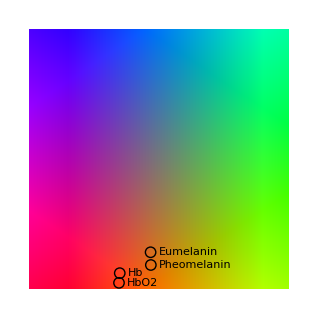
```mathematica
LCaCbSpaceImage=-Graphics-;
```

```mathematica
Clear[uProbFun]
uProbFun=Table[setProbFun[colorSpaceRules[[i]]],{i,1,5}];
```

```mathematica
LCaCbSpaceImageData=Table[processImage[ImageData[LCaCbSpaceImage,"Byte"],{},{uProbFun[[i,1]]},colorSpaceRules[[i]]],{i,1,5}];
```

```mathematica
GraphicsRow[Table[SetAlphaChannel[LCaCbSpaceImage,Image[LCaCbSpaceImageData[[sig,2,All,All,4]]]],{sig,1,5}]]
```

#### The Probability Function Results

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
GraphicsGrid[Table[Column[{Image[imgSmallLCaCbData[[j,i,All,All]],ColorSpace->"RGB"],Row[{"  ",label[[j]],"  ",i,"σ"}]}],{j,1,3},{i,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
GraphicsGrid[Table[Column[{Image[imgSmallLCaCbData[[j,i,All,All,4]]],Row[{"  ",label[[j]],"  ",i,"σ"}]}],{j,1,3},{i,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
GraphicsGrid[Table[Column[{SetAlphaChannel[imgs[[j]],Image[imgSmallLCaCbData[[j,i,All,All,4]]]],Row[{"  ",label[[j]],"  ",i,"σ"}]}],{j,1,3},{i,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

#### The Probability Function

After Redistribution we have two new spaces in which to express the stats parameters. The 0-dstMax range and the new 0-1 range where 0 and 1 correspond to different positions in the original unit space becase of the contraction of the information. The mean values are at the half way point in both

```mathematica
cd=dstMax/2
μd={0.5,0.5,0.5}
```

the standard deviations are scaled by the regions which are kept and the new ranges.

```mathematica
sd=dstMax s/(Λ[[All,2]]-Λ[[All,1]])
σd=σ/(λ[[All,2]]-λ[[All,1]])
```

The probability is the product of these two Gaussians

```mathematica
Row[{Plot[Exp[-(x-dstMax[[2]]/2)^2/(2 (sd[[2]])^2)],{x,0,dstMax[[2]]}],
Plot[Exp[-(x-dstMax[[3]]/2)^2/(2 (sd[[3]])^2)],{x,0,dstMax[[3]]}]}]
Row[{Plot[Exp[-(x-1/2)^2/(2( σd[[2]])^2)],{x,0,1}],
Plot[Exp[-(x-1/2)^2/(  2 (σd[[3]])^2)],{x,0,1}]}]
```

```mathematica
Clear[pxl]
{uProbFun,probFun } =setProbFun[colorSpaceRules[[1]]];
Row[{"ℙ = ",uProbFun[{L,Ca,Cb}]}]
```

### The Region Function

The region catagorization function is applied before the redistribution function.

#### The Unreliable region Function

```mathematica
mAEPath1=WOBOPathLCaCb[minorAxisEnds[[1]],1,θ];
mAEPath2=WOBOPathLCaCb[minorAxisEnds[[2]],1,θ];
MMBO=chMM[{Sequence@@(Map[slack[#,OptionValue[Slack]]&,chMM[(mAEPath1[[1;;3]])],{2}]),Sequence@@(Map[slack[#,OptionValue[Slack]]&,chMM[(mAEPath2[[1;;3]])],{2}])}];
MMWO=chMM[{Sequence@@(Map[slack[#,OptionValue[Slack]]&,chMM[(mAEPath1[[4;;6]])],{2}]),Sequence@@(Map[slack[#,OptionValue[Slack]]&,chMM[(mAEPath2[[4;;6]])],{2}])}];
```

```mathematica
Clear[unreliableFun];
unreliableFun=setUnreliableFun[colorSpaceRules[[1]],1,Slack->0.1,qRange->False];
Row[{"𝕃 = ",unreliableFun[L,Ca,Cb]}]
```

```mathematica
Clear[unreliableFun];
unreliableFun=setUnreliableFun[colorSpaceRules[[1]],1,Slack->0.1,qRange->False]
```

First we need to define the regions which suffer from whiteout and blackout. We take the ends of the minor axis and find the WOBO path theoretically for these points.

```mathematica
μ="μ"/.colorSpaceRules[[1]];
σ="σ"/.colorSpaceRules[[1]];
θ="θ"/.colorSpaceRules[[1]];
minorAxisEnds={μ-{0,2 σ[[2]],2 σ[[3]]},μ+{0,-2 σ[[2]],2 σ[[3]]}}
mAEPath1=WOBOPathLCaCb[minorAxisEnds[[1]],1,θ]
mAEPath2=WOBOPathLCaCb[minorAxisEnds[[2]],1,θ]
chMM=Function[{list},({MapThread[Min,list],MapThread[Max,list]})];
MMBO=chMM[{Sequence@@(Map[slack,chMM[(mAEPath1[[1;;3]])],{2}]),Sequence@@(Map[slack,chMM[(mAEPath2[[1;;3]])],{2}])}]
MMWO=chMM[{Sequence@@(Map[slack,chMM[(mAEPath1[[4;;6]])],{2}]),Sequence@@(Map[slack,chMM[(mAEPath2[[4;;6]])],{2}])}]
```

The Limits in the unit space for unreliable WOBO values are

```mathematica
LWOBOLimits={MMBO[[2,1]],MMWO[[1,1]]}
CaWOBOLimits={Min[{MMBO[[1,2]],MMWO[[1,2]]}],Max[{MMBO[[2,2]],MMWO[[2,2]]}]}
CbWOBOLimits={Min[{MMBO[[1,3]],MMWO[[1,3]]}],Max[{MMBO[[2,3]],MMWO[[2,3]]}]}
Clear[L,Ca,Cb]
unreliableFun = Function[{L,Ca,Cb},Evaluate[(!(LWOBOLimits[[1]]<L<LWOBOLimits[[2]]))&&CaWOBOLimits[[1]]<Ca<CaWOBOLimits[[2]]&&CbWOBOLimits[[1]]<Cb<CbWOBOLimits[[2]]]]
```

```mathematica
Block[{L,WO,BO,RGBCubeRegion,LWOBOLimitsL,CaWOBOLimitsL,CbWOBOLimitsL,WORegion,BORegion,LCaCbTransform},
L=("L"/.colorSpaceRules[[1]]);
LWOBOLimitsL={MMBO[[1,1]],MMWO[[2,1]]}L[[1]];
CaWOBOLimitsL=(CaWOBOLimits-{1/2,1/2})L[[2]];
CbWOBOLimitsL=(CbWOBOLimits-{1/2,1/2})L[[3]];
WORegion = Cuboid[{LWOBOLimits[[1]],CaWOBOLimitsL[[1]],CbWOBOLimitsL[[1]]},{L[[1]],CaWOBOLimitsL[[2]],CbWOBOLimitsL[[2]]}];
BORegion = Cuboid[{0,CaWOBOLimitsL[[1]],CbWOBOLimitsL[[1]]},{LWOBOLimits[[2]],CaWOBOLimitsL[[2]],CbWOBOLimitsL[[2]]}];
LCaCbTransform=Composition[RotationTransform[LCaCbθ,{1,0,0}],RotationTransform[-ArcTan[1/Sqrt[2]],{0,0,1}],RotationTransform[Pi/4,{0,1,0}]];
RGBCubeRegion=TransformedRegion[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform];
WO=RegionIntersection[WORegion,RGBCubeRegion];
BO=RegionIntersection[BORegion,RGBCubeRegion];

Row[{RegionPlot3D[{TransformedRegion[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform],WO,BO},PlotPoints->125,PlotRange->{{0,L[[1]]},{-L[[2]]/2,L[[2]]/2},{-L[[3]]/2,L[[3]]/2}},PlotStyle->{Directive[Yellow,Opacity[0.5]],Directive[White,Opacity[0.5]],Directive[Black,Opacity[0.5]]},Mesh->None,ViewVertical->{1,0,0}],
RegionPlot3D[{TransformedRegion[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform],WORegion,BORegion},PlotPoints->125,PlotRange->{{0,L[[1]]},{-L[[2]]/2,L[[2]]/2},{-L[[3]]/2,L[[3]]/2}},PlotStyle->{Directive[Yellow,Opacity[0.5]],Directive[White,Opacity[0.5]],Directive[Black,Opacity[0.5]]},Mesh->None,ViewVertical->{1,0,0}],
Graphics3D[{Directive[Yellow,Opacity[0.5]],GeometricTransformation[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform],Directive[White,Opacity[0.5]],WORegion,Directive[Black,Opacity[0.5]],BORegion},ViewVertical->{1,0,0}]}]
]
```

### The Partition Function

#### The Color Partition Function

```mathematica
{colorTargetSquare,colorTargetElliptical} = setColorTargetFun[colorSpaceRules[[1]],2,qRange->False];
```

We now define a function which catagorizes a pixel value as in the target color region. There are two options a rectangular segnentation or an eliptical segmentation.

```mathematica
setColorTargetFun[colorSpaceRules[[1]],2,qRange->True][[1]]
```

```mathematica
colorTargetSquare[L,Ca,Cb]//TraditionalForm
```

```mathematica
showColorTargetFun[colorSpaceRules[[1]],5]
```

The Elliptical partitioning function

```mathematica
colorTargetElliptical[L,Ca,Cb]//TraditionalForm
```

```mathematica
Quiet[(RegionPlot[{colorTargetSquare[0.5,Ca,Cb],colorTargetElliptical[0.5,Ca,Cb]},{Ca,"μ"[[2]]-5 "σ"[[2]],"μ"[[2]]+5 "σ"[[2]]},{Cb,"μ"[[3]]-5 "σ"[[2]],"μ"[[3]]+5 "σ"[[2]]}])/.colorSpaceRules[[1]],{Part::partd,RegionPlot::plln}]
```

#### The Region Function

```mathematica
regionFun[ℂ,𝕃]//TraditionalForm
```

The region Classifier

```mathematica
"qRsRange"/.colorSpaceRules[[1]]
```

```mathematica
rgnClassFun=RegionClassifier[colorSpaceRules[[1]],1,qRange->False,Slack->0];
rgnClass[pts_List]:=rgnClassFun[Sequence@@pts];
rgnClass[{L,Ca,Cb}]//TraditionalForm
```

```mathematica
grfx=Block[{res=0.01},
Table[cls=rgnClassFun[l,Ca,Cb];If[cls>0,{{Red,Blue,Green}[[cls]],Cuboid[{l,Ca,Cb},{l+res,Ca+res,Cb+res}]}],{l,0,1,res},{Ca,0,1,res},{Cb,0,1,res}]
];
```

```mathematica
Graphics3D[{{EdgeForm[Black],FaceForm[],Cuboid[{0,0,0},{1,1,1}]},EdgeForm[],Opacity[0.6],grfx},ViewVertical->{1, 0, 0}]
```

### Results

```mathematica
Clear[unreliableFun];
unreliableFun=setUnreliableFun[colorSpaceRules[[1]],1,Slack->0.1,qRange->False];
Row[{"𝕃 = ",unreliableFun[L,Ca,Cb]}]
```

```mathematica
imgLCaCbDataClassified[[1,200,200,1;;3]]/("qRsRange"/.colorSpaceRules[[1]])
N[%]
fromLCaCb[%]
RGBColor[%]
```

```mathematica
Max[imgSmallLCaCbDataClassified[[All,All,1;;3]]]
```

```mathematica
Dimensions[imgSmallLCaCbDataClassified]
```

```mathematica
Image[imgSmallLCaCbDataClassified[[2,1,2,All,All,1;;3]]]
```

```mathematica
"dstMax"/.colorSpaceRules[[1]]
```

```mathematica
"fSs"/.colorSpaceRules[[1]]
```

```mathematica
Max[ImageData[imgs[[2]],"Byte"]]
```

```mathematica
("qRsRange"/.colorSpaceRules[[1]])
```

```mathematica
Round[imgSmallLCaCbDataClassified[[2,1,83,303,1;;3]]("qRsRange"/.colorSpaceRules[[1]])]
```

```mathematica
reliableFunSquare[Sequence@@(imgSmallLCaCbDataClassified[[2,1,62,315,1;;3]])]
```

```mathematica
imgSmallLCaCbDataClassified[[2,1,1,62,315,1;;3]]
```

```mathematica
regionClassifier[{678,13584,16254}]
```

```mathematica
imgSmallLCaCbDataClassified[[2,1,62,315,1;;3]]
regionClassifier[{654,26341,20400}]
```

```mathematica
imgSmallLCaCbDataClassified=processImage[ImageData[imgs[[1]],"Byte"],{rgnClass},{rgnClass},colorSpaceRules[[1]]];
```

```mathematica
imgClass=imgSmallLCaCbDataClassified[[All,All,4]];
```

```mathematica
imgClassColor=imgClass/. {0->Black,1->Red,2->Blue,3->Green};
```

```mathematica
Position[imgSmallLCaCbDataClassified[[2,1,All,All,4]],1]
```

```mathematica
Dimensions[imgSmallLCaCbDataClassified]
```

```mathematica
GraphicsRow[{Image[imgSmallLCaCbDataClassified[[All,All,1;;3]]],Image[imgSmallLCaCbDataClassified[[All,All,4]]/. {0->Black,1->Red,2->Blue,3->Green}]}]
```

```mathematica
imgSmallLCaCbDataClassified[[1,1,10;;20,10;;20,4]]
```

```mathematica
Dimensions[imgSmallLCaCbDataClassified]
```

```mathematica
Image[imgSmallLCaCbDataClassified[[10;;200,10;;200,1;;3]]]
```

```mathematica
Position[imgSmallLCaCbDataClassified[[All,All,1;;3]],n_/;!NumberQ[#]&]
```

```mathematica
Max[imgSmallLCaCbDataClassified[[All,All,1;;3]]]
```

```mathematica
imgSmallLCaCbDataClassified=Table[processImage[ImageData[imgs[[j]],"Byte"],{regionClassifier},{},colorSpaceRules[[i]]],{j,1,3},{i,1,5}];
```

## The parameterised distribution function.

```mathematica
Definition[dis]
```

```mathematica
dis[ mKδL 2^(1-n)x ,mKδL 2^n  σ,mKδL 2^n μ ,-mKδL 2^(n-1) ,mKδL 2^(n-1),0,2^n]
```

```mathematica
Clear[σ,μ,δμ]
Block[{σ,μ},
FullSimplify[dis[ mKδL 2^(1-n)x ,mKδL 2^n  σ,mKδL 2^n (μ) ,-mKδL 2^(n-1) ,mKδL 2^(n-1),0,2^n]]
]
```

```mathematica
-(2^n (Erf[(1+2 μ)/(2 √2 σ)]+Erf[(2^(1-2 n) x-μ)/(σ √2)]))/(Erf[(-1+2 μ)/(2 √2 σ)]-Erf[(1+2 μ)/(2 √2 σ)])
```

```mathematica
N[2Sqrt[2/3]]
```

```mathematica
Reduce[2^(-1/2-2 n) (2 x-4^n μ)==(2^(1-2 n) x-μ)/(√2)]
```

```mathematica
Expand[2^(-1/2-2 n) (2 x-4^n μ)]
```

```mathematica
(√2)/2(2^(1-2 n) x-μ)
```

```mathematica
Clear[σ,μ,δμ]
Block[{σ,μ},
FullSimplify[dis[ a x ,a   σ,a  μ ,a sMin ,a sMax,0,2^n]]
]
```

## Junk

```mathematica
Clear[L,Ca,Cb]
reliableFunElliptical = Function[{L,Ca,Cb},Evaluate[(Ca-μ[[2]])^2/( σ[[2]])^2 + (Cb-μ[[3]])^2/( σ[[3]])^2<=1]]
```

```mathematica
{toLCaCb, fromLCaCb}=setLCaCb[LCaCbθ];
```

```mathematica
μRGB=fromLCaCb[c/255]
cRGB=255  μRGB
WOBOLimits=WOBOPathLCaCb[μRGB][[3;;4,1]]
qRsRange="qRsRange"/.colorSpaceRules[[2]];
unreliableFun=Function[{pxl},If[(pxl[[1]]<qRsRange[[2]] WOBOLimits[[1]]|| pxl[[1]]>qRsRange[[3]] WOBOLimits[[2]])&&pxl[[2]]<128,1,0]]
```

```mathematica
Clear[pxl]
path=WOBOPathLCaCb[μRGB]
pathMax=MapThread[Max,path]
pathMin=MapThread[Min,path]
WOBOLimits=path[[3;;4,1]]
unreliableFun=Function[{pxl},Evaluate[(pxl[[1]]<qRsRange[[1]] WOBOLimits[[1]] ||pxl[[1]]>qRsRange[[1]] WOBOLimits[[2]]) && (qRsRange[[2]] pathMin[[2]]<=pxl[[2]]≤ qRsRange[[2]] pathMax[[2]])&&(qRsRange[[3]] pathMin[[3]]<=pxl[[3]]≤ qRsRange[[3]] pathMax[[3]])]]
probFun=Function[{Ca,Cb,CaMin,CaMax,CbMin,CbMax},
1/2-Sqrt[(((Ca-CaMin)/(CaMax-CaMin)-1/2 )^2 +((Cb-CbMin)/(CbMax-CbMin)-1/2)^2)]
];
```

```mathematica
pxl
```

```mathematica
path[[3;;4,1]]
```

```mathematica
qRsRange
```

```mathematica
qRsRange WOBOLimits[[1]]
```

```mathematica
MapThread[Less,{{0.5,0.2,0.3},{0.6,0.3,0.4}}]
```

```mathematica
μRGB=fromLCaCb[c/255]
cRGB=255  μRGB
WOBOLimits=WOBOPathLCaCb[μRGB][[3;;4,1]]
unreliableFun=Function[{pxl},If[(pxl[[1]]<255 WOBOLimits[[1]]|| pxl[[1]]>255 WOBOLimits[[2]])&&pxl[[2]]<128,1,0]]
```

```mathematica
imgData=ImageData[imgSmall,"Byte"];
```

```mathematica
probFun=Function[{Ca,Cb,CaMin,CaMax,CbMin,CbMax},
1/2-Max[Abs[({(Ca-CaMin)/(CaMax-CaMin)-1/2 ,(Cb-CbMin)/(CbMax-CbMin)-1/2})]]
];
```

```mathematica
probFun[Ca,Cb,0,CaMax,CbMin,CbMax]
```

```mathematica
FullSimplify[1/2-Max[Abs[-1/2+(Ca-CaMin)/(CaMax-CaMin)],Abs[-1/2+(Cb-CbMin)/(CbMax-CbMin)]]]
```

```mathematica
unreliableFun
```

```mathematica
BinaryNumberSigned[num_,digits_]:=NumberForm[BaseForm[num,2],digits-1,DigitBlock->4,NumberPadding->{"0","0"},SignPadding->True,NumberSigns->{"-","+"}];
```

```mathematica
BinaryNumberSigned[2^(-2+8)-2^(-2+2 8),16]
```

```mathematica
Simplify[(2^(m)-1)/(2^n-1)]
```

```mathematica
qRsMax=Expand[{0, 2^(n-2) (2^n-1),2^(n-2) (2^n-1)}];
MatrixForm[qRsMax]
```

```mathematica
2^{2 n-2}-2^{n-2}-(2^(-2+n)-2^(-2+2 n))
```

```mathematica
Expand[2 2^(n-2) (2^n-1)]
```

```mathematica
Block[{n=8},

δ=("δ"/.distroRules);
K=("K"/.distroRules);
L="L"/.distroRules;
λ="λ"/.distroRules;
ωp="ωp"/.distroRules;
qRsMin={0,- 2^(n-2) (2^n-1),- 2^(n-2) (2^n-1)};
qRsMax={0, 2^(n-2) (2^n-1),2^(n-2) (2^n-1)};
qRsRange={3 2^n,2 2^(n-2) (2^n-1),2 2^(n-2) (2^n-1)};
Λ=Round[2^n λ]; Λq=Round[qRsRange λ];
Ωp=Round[2^n λ]; Ωpq=Round[qRsRange λ];
Qdisc=Map[(2^3/2^n<#)&,({1,1,1}-λ[[All,2]]+λ[[All,1]])];
Qdist=Map[(2^3/2^n<#)&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])];
Qkeep=Map[(1/2^n<#)&,(ωp[[All,2]]-ωp[[All,1]])];
S=MapThread[Min,{δ K,N[L]}] {1/3,2^(1-n),2^(1-n)};
dstMax=Table[Round[disFun[[i]][qRsRange[[i]]]],{i,1,3}];


Column[{Grid[{{Row[{"θ = ",Θ+δθ," ≃ ",(2 π)/7}],SpanFromLeft,SpanFromLeft},{TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ","θ"," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA[47,8],Θ +thetaExtremaB[43,8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA[49,8],Θ +thetaExtremaB[45,8]}]}]]
}},Spacings->2,Frame->All,Alignment->Left],
Row[{"dstMax = ",MatrixForm@dstMax}],
Row[{qR["2 π"]," = ",MatrixForm[qR[(2 π)/7]]}],
Row[{fSs["2 π"]," = ",MatrixForm[fSs[(2 π)/7]]}],
Row[{"S = ",MatrixForm[S]}],
Row[{2^n Subscript["Q", "discard"]," = ",MatrixForm[Round[2^n ({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "distribute"]," = ",MatrixForm[Round[2^n(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "keep"]," = ",MatrixForm[Round[2^n(ωp[[All,2]]-ωp[[All,1]])]]}],
Row[{ Subscript["τ", "discard"]," = ",2^3/2^n}],
Row[{Subscript["τ", "distribute"]," = ",2^3/2^n}],
Row[{Subscript["τ", "keep"]," = ",1/2^n}],
Row[{ Subscript["Q", "discard"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{Subscript["Q", "distribute"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{Subscript["Q", "keep"]," = ",MatrixForm[Map[(Row[{1/2^n," < ",#}] )&,(ωp[[All,2]]-ωp[[All,1]])]]," = ",MatrixForm[Map[(1/2^n<#)&,(ωp[[All,2]]-ωp[[All,1]])]]}],
Grid[{{"","0-1","0-255","qRange"},{"λ",MatrixForm@λ,MatrixForm@Λ,MatrixForm@Λq},{"ω",MatrixForm@ωp,MatrixForm@Ωp,MatrixForm@Ωpq}}]
}]
]
```

```mathematica
Plot[(1-1/2Abs[x]),{x,-2,2}]
Plot[(1-1/4Abs[y]),{y,-4,4}]
ContourPlot[Min[(1-1/2Abs[x]),(1-1/4Abs[y])],{x,-2,2},{y,-4,4}]
ContourPlot[Sqrt[(1/2Abs[x])^2+(1/4Abs[y])^2],{x,-2,2},{y,-4,4}]
```